{-(-2 (-5+3 √5))^(1/3),(2 (-5+3 √5))^(1/3),(-1)^(2/3) (2 (-5+3 √5))^(1/3),(-2 (5+3 √5))^(1/3),-(2 (5+3 √5))^(1/3),-(-1)^(2/3) (2 (5+3 √5))^(1/3)}

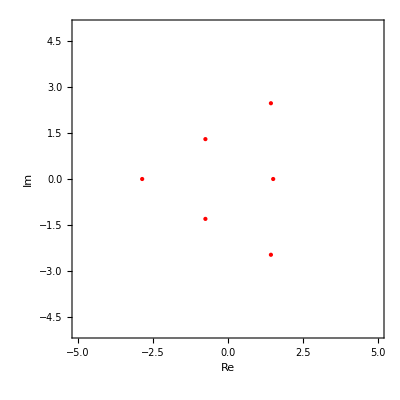

```mathematica
m=1;
a=CoefficientList[Series[Exp[z  ϵ-2^(2 m)/(2 m+1) ϵ^(2 m+1)],{ϵ,0,10}],ϵ];
aa=Part[a,{1,2,3,4,5,6}];
aa[[0]]=0;
Det[{{aa[[2]],aa[[1]],aa[[0]]},{aa[[4]],aa[[3]],aa[[2]]},{aa[[6]],aa[[5]],aa[[4]]}}]//FullSimplify;
q =Wronskian[({aa[[2]],aa[[4]],aa[[6]]}),z]//FullSimplify;
s = Solve[q == 0,z];
rt = Flatten[Values[s]]
ComplexListPlot[rt,PlotRange->{{-5,5},{-5,5}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Red,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}]
```

```mathematica
{1,z,z^2/2,z^3/6,z^4/24,1/120 (-384+z^5),1/720 (-2304 z+z^6),(-8064 z^2+z^7)/5040,(-21504 z^3+z^8)/40320,(-48384 z^4+z^9)/362880,(18579456-96768 z^5+z^10)/3628800}
```

{1,z,z^2/2,z^3/6,z^4/24,1/120 (-384+z^5),1/720 (-2304 z+z^6),(-8064 z^2+z^7)/5040,(-21504 z^3+z^8)/40320,(-48384 z^4+z^9)/362880,(18579456-96768 z^5+z^10)/3628800}

```mathematica
k1=z0^3/3;
k2=z0^5/5;
k3=z0^7/7;
k4=z0^9/9;
k5=z0^11/11;

a=CoefficientList[Series[Exp[z  ϵ+k1 ϵ^3 + k2 ϵ^5 + k3 ϵ^7 +k4 ϵ^ 9+ k5 ϵ^11+ 7 ϵ^13 + 8 ϵ^15],{ϵ,0,10}],ϵ];
aa=Part[a,{1,2,3,4,5,6,7,8,9,10}];
aa[[0]]=0;
q =Wronskian[({aa[[2]],aa[[4]],aa[[6]]}),z]//FullSimplify
q =Wronskian[({aa[[2]],aa[[4]],aa[[6]],aa[[8]]}),z]//FullSimplify
q =Wronskian[({aa[[2]],aa[[4]],aa[[6]],aa[[8]],aa[[10]]}),z]//FullSimplify
```

1/45 (z^6-5 z^3 z0^3+9 z z0^5-5 z0^6)

((z-z0)^6 (z^4+6 z^3 z0+21 z^2 z0^2+41 z z0^3+36 z0^4))/4725

((z-z0)^10 (z^5+10 z^4 z0+55 z^3 z0^2+185 z^2 z0^3+365 z z0^4+329 z0^5))/4465125

{-√(2 (-1+√6)),√(2 (-1+√6)),-ⅈ √(2 (1+√6)),ⅈ √(2 (1+√6))}

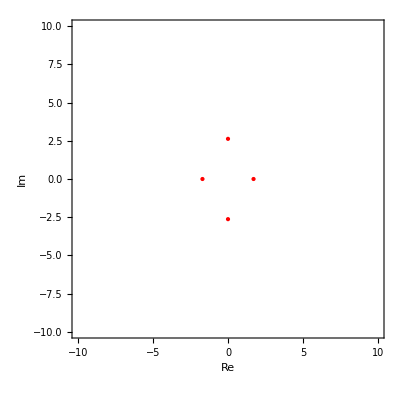

```mathematica
a=CoefficientList[Series[Exp[z  ϵ+ϵ^2 + 2 ϵ^4 + 3 ϵ^5 + 4 ϵ^7 ],{ϵ,0,10}],ϵ];
aa=Part[a,{1,2,3,4,5,6,7,8,9,10}];
aa[[0]]=0;
q =Wronskian[({aa[[2]],aa[[5]]}),z]//FullSimplify;s = Solve[q == 0,z];

rt = Flatten[Values[s]]
ComplexListPlot[rt,PlotRange->{{-10,10},{-10,10}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Red,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}]
```

{Root-1.61-1.38 ⅈRoot[120-80 #1-20 #1^2+10 #1^4+#1^6&,1]-1.6129078151444882,Root-1.61+1.38 ⅈRoot[120-80 #1-20 #1^2+10 #1^4+#1^6&,2]-1.6129078151444882,Root0.198-3.55 ⅈRoot[120-80 #1-20 #1^2+10 #1^4+#1^6&,3]0.19813704828633663,Root0.198+3.55 ⅈRoot[120-80 #1-20 #1^2+10 #1^4+#1^6&,4]0.19813704828633663,Root1.41-0.308 ⅈRoot[120-80 #1-20 #1^2+10 #1^4+#1^6&,5]1.4147707668581517,Root1.41+0.308 ⅈRoot[120-80 #1-20 #1^2+10 #1^4+#1^6&,6]1.4147707668581517}

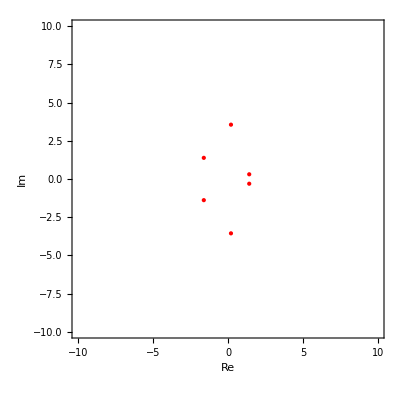

```mathematica
a=CoefficientList[Series[Exp[z  ϵ+ ϵ^2 +  ϵ^4 +  ϵ^5 +  ϵ^7 ],{ϵ,0,10}],ϵ];
aa=Part[a,{1,2,3,4,5,6,7,8,9,10}];
aa[[0]]=0;
q =Wronskian[({aa[[3]],aa[[6]]}),z]//FullSimplify;
s = Solve[q == 0,z];

rt = Flatten[Values[s]]
ComplexListPlot[rt,PlotRange->{{-10,10},{-10,10}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Red,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}]
```

{Root-2.18+0.606 ⅈRoot[{1+#1^2&,-80-40 #1-80 #1 #2-20 #2^2-40 #1 #2^2+10 #1 #2^4+#2^6&},{2,1}]-2.1826168204636622,Root-1.58+2.67 ⅈRoot[{1+#1^2&,-80-40 #1-80 #1 #2-20 #2^2-40 #1 #2^2+10 #1 #2^4+#2^6&},{2,2}]-1.5830503223520116,Root-0.798-1.40 ⅈRoot[{1+#1^2&,-80-40 #1-80 #1 #2-20 #2^2-40 #1 #2^2+10 #1 #2^4+#2^6&},{2,3}]-0.7981077260744072,Root-0.0404+0.866 ⅈRoot[{1+#1^2&,-80-40 #1-80 #1 #2-20 #2^2-40 #1 #2^2+10 #1 #2^4+#2^6&},{2,4}]-0.04037297588429641,Root2.04-2.90 ⅈRoot[{1+#1^2&,-80-40 #1-80 #1 #2-20 #2^2-40 #1 #2^2+10 #1 #2^4+#2^6&},{2,5}]2.0398698494255996,Root2.56+0.151 ⅈRoot[{1+#1^2&,-80-40 #1-80 #1 #2-20 #2^2-40 #1 #2^2+10 #1 #2^4+#2^6&},{2,6}]2.5642779953487778}

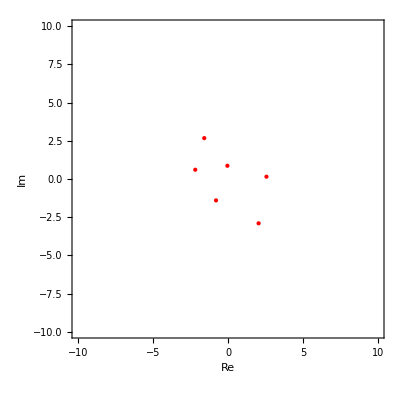

```mathematica
a=CoefficientList[Series[Exp[z  ϵ+ ⅈ ϵ^2 + ⅈ  ϵ^4 +ⅈ   ϵ^5 +  ⅈ ϵ^7 ],{ϵ,0,10}],ϵ];
aa=Part[a,{1,2,3,4,5,6,7,8,9,10}];
aa[[0]]=0;
q =Wronskian[({aa[[3]],aa[[6]]}),z]//FullSimplify;
s = Solve[q == 0,z];

rt = Flatten[Values[s]]
ComplexListPlot[rt,PlotRange->{{-10,10},{-10,10}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Red,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}]
```

{Root-3.43+2.40 ⅈRoot[{1+#1^2&,-5908952000+31932316800 #1-16632000000 #2+3548160000 #1 #2+10398240000 #2^2-4488792000 #1 #2^2+3592512000 #2^3+4989600000 #1 #2^3+1841439600 #2^4+2317896000 #1 #2^4+299376000 #2^5+279417600 #1 #2^5+209563200 #2^6-291060000 #1 #2^6-38491200 #1 #2^7-40540500 #2^8-15717240 #1 #2^8+2619540 #1 #2^10+56133 #2^12&},{2,1}]-3.4288085516234825,Root-3.33+0.195 ⅈRoot[{1+#1^2&,-5908952000+31932316800 #1-16632000000 #2+3548160000 #1 #2+10398240000 #2^2-4488792000 #1 #2^2+3592512000 #2^3+4989600000 #1 #2^3+1841439600 #2^4+2317896000 #1 #2^4+299376000 #2^5+279417600 #1 #2^5+209563200 #2^6-291060000 #1 #2^6-38491200 #1 #2^7-40540500 #2^8-15717240 #1 #2^8+2619540 #1 #2^10+56133 #2^12&},{2,2}]-3.3264561329862214,Root-2.82+4.46 ⅈRoot[{1+#1^2&,-5908952000+31932316800 #1-16632000000 #2+3548160000 #1 #2+10398240000 #2^2-4488792000 #1 #2^2+3592512000 #2^3+4989600000 #1 #2^3+1841439600 #2^4+2317896000 #1 #2^4+299376000 #2^5+279417600 #1 #2^5+209563200 #2^6-291060000 #1 #2^6-38491200 #1 #2^7-40540500 #2^8-15717240 #1 #2^8+2619540 #1 #2^10+56133 #2^12&},{2,3}]-2.820678918507854,Root-1.58-1.80 ⅈRoot[{1+#1^2&,-5908952000+31932316800 #1-16632000000 #2+3548160000 #1 #2+10398240000 #2^2-4488792000 #1 #2^2+3592512000 #2^3+4989600000 #1 #2^3+1841439600 #2^4+2317896000 #1 #2^4+299376000 #2^5+279417600 #1 #2^5+209563200 #2^6-291060000 #1 #2^6-38491200 #1 #2^7-40540500 #2^8-15717240 #1 #2^8+2619540 #1 #2^10+56133 #2^12&},{2,4}]-1.5845488436787332,Root-1.23+2.68 ⅈRoot[{1+#1^2&,-5908952000+31932316800 #1-16632000000 #2+3548160000 #1 #2+10398240000 #2^2-4488792000 #1 #2^2+3592512000 #2^3+4989600000 #1 #2^3+1841439600 #2^4+2317896000 #1 #2^4+299376000 #2^5+279417600 #1 #2^5+209563200 #2^6-291060000 #1 #2^6-38491200 #1 #2^7-40540500 #2^8-15717240 #1 #2^8+2619540 #1 #2^10+56133 #2^12&},{2,5}]-1.232575844841598,Root-1.09+0.769 ⅈRoot[{1+#1^2&,-5908952000+31932316800 #1-16632000000 #2+3548160000 #1 #2+10398240000 #2^2-4488792000 #1 #2^2+3592512000 #2^3+4989600000 #1 #2^3+1841439600 #2^4+2317896000 #1 #2^4+299376000 #2^5+279417600 #1 #2^5+209563200 #2^6-291060000 #1 #2^6-38491200 #1 #2^7-40540500 #2^8-15717240 #1 #2^8+2619540 #1 #2^10+56133 #2^12&},{2,6}]-1.0892345581412988,Root0.541-3.46 ⅈRoot[{1+#1^2&,-5908952000+31932316800 #1-16632000000 #2+3548160000 #1 #2+10398240000 #2^2-4488792000 #1 #2^2+3592512000 #2^3+4989600000 #1 #2^3+1841439600 #2^4+2317896000 #1 #2^4+299376000 #2^5+279417600 #1 #2^5+209563200 #2^6-291060000 #1 #2^6-38491200 #1 #2^7-40540500 #2^8-15717240 #1 #2^8+2619540 #1 #2^10+56133 #2^12&},{2,7}]0.541049814520841,Root0.608+1.60 ⅈRoot[{1+#1^2&,-5908952000+31932316800 #1-16632000000 #2+3548160000 #1 #2+10398240000 #2^2-4488792000 #1 #2^2+3592512000 #2^3+4989600000 #1 #2^3+1841439600 #2^4+2317896000 #1 #2^4+299376000 #2^5+279417600 #1 #2^5+209563200 #2^6-291060000 #1 #2^6-38491200 #1 #2^7-40540500 #2^8-15717240 #1 #2^8+2619540 #1 #2^10+56133 #2^12&},{2,8}]0.6083121518313354,Root1.30-0.718 ⅈRoot[{1+#1^2&,-5908952000+31932316800 #1-16632000000 #2+3548160000 #1 #2+10398240000 #2^2-4488792000 #1 #2^2+3592512000 #2^3+4989600000 #1 #2^3+1841439600 #2^4+2317896000 #1 #2^4+299376000 #2^5+279417600 #1 #2^5+209563200 #2^6-291060000 #1 #2^6-38491200 #1 #2^7-40540500 #2^8-15717240 #1 #2^8+2619540 #1 #2^10+56133 #2^12&},{2,9}]1.301061943253127,Root3.54-4.92 ⅈRoot[{1+#1^2&,-5908952000+31932316800 #1-16632000000 #2+3548160000 #1 #2+10398240000 #2^2-4488792000 #1 #2^2+3592512000 #2^3+4989600000 #1 #2^3+1841439600 #2^4+2317896000 #1 #2^4+299376000 #2^5+279417600 #1 #2^5+209563200 #2^6-291060000 #1 #2^6-38491200 #1 #2^7-40540500 #2^8-15717240 #1 #2^8+2619540 #1 #2^10+56133 #2^12&},{2,10}]3.542684284033761,Root3.68+0.456 ⅈRoot[{1+#1^2&,-5908952000+31932316800 #1-16632000000 #2+3548160000 #1 #2+10398240000 #2^2-4488792000 #1 #2^2+3592512000 #2^3+4989600000 #1 #2^3+1841439600 #2^4+2317896000 #1 #2^4+299376000 #2^5+279417600 #1 #2^5+209563200 #2^6-291060000 #1 #2^6-38491200 #1 #2^7-40540500 #2^8-15717240 #1 #2^8+2619540 #1 #2^10+56133 #2^12&},{2,11}]3.682644251698242,Root3.81-1.66 ⅈRoot[{1+#1^2&,-5908952000+31932316800 #1-16632000000 #2+3548160000 #1 #2+10398240000 #2^2-4488792000 #1 #2^2+3592512000 #2^3+4989600000 #1 #2^3+1841439600 #2^4+2317896000 #1 #2^4+299376000 #2^5+279417600 #1 #2^5+209563200 #2^6-291060000 #1 #2^6-38491200 #1 #2^7-40540500 #2^8-15717240 #1 #2^8+2619540 #1 #2^10+56133 #2^12&},{2,12}]3.806550404441882}

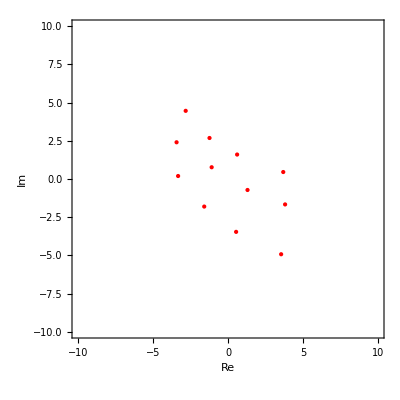

```mathematica
a=CoefficientList[Series[Exp[z  ϵ+ (5ⅈ)/3 ϵ^2 + (5ⅈ)/5   ϵ^4 +(5ⅈ)/7  ϵ^5 +  (5ⅈ)/9 ϵ^7  +(5ⅈ)/11  ϵ^8 + (5ⅈ)/13  ϵ^10],{ϵ,0,10}],ϵ];
aa=Part[a,{1,2,3,4,5,6,7,8,9,10}];
aa[[0]]=0;
q =Wronskian[({aa[[2]],aa[[5]],aa[[8]]}),z]//FullSimplify;
s = Solve[q == 0,z];

rt = Flatten[Values[s]]
ComplexListPlot[rt,PlotRange->{{-10,10},{-10,10}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Red,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}]
```

{Root1.46Root[123200-89600 #1+190400 #1^2-134400 #1^3+2800 #1^4+4480 #1^5-1120 #1^6-960 #1^7-20 #1^8+28 #1^10+#1^12&,1]1.456932168165586,Root3.38Root[123200-89600 #1+190400 #1^2-134400 #1^3+2800 #1^4+4480 #1^5-1120 #1^6-960 #1^7-20 #1^8+28 #1^10+#1^12&,2]3.382830271802527,Root-3.00-1.34 ⅈRoot[123200-89600 #1+190400 #1^2-134400 #1^3+2800 #1^4+4480 #1^5-1120 #1^6-960 #1^7-20 #1^8+28 #1^10+#1^12&,3]-3.0034760307499195,Root-3.00+1.34 ⅈRoot[123200-89600 #1+190400 #1^2-134400 #1^3+2800 #1^4+4480 #1^5-1120 #1^6-960 #1^7-20 #1^8+28 #1^10+#1^12&,4]-3.0034760307499195,Root-1.75-3.59 ⅈRoot[123200-89600 #1+190400 #1^2-134400 #1^3+2800 #1^4+4480 #1^5-1120 #1^6-960 #1^7-20 #1^8+28 #1^10+#1^12&,5]-1.7520229871411486,Root-1.75+3.59 ⅈRoot[123200-89600 #1+190400 #1^2-134400 #1^3+2800 #1^4+4480 #1^5-1120 #1^6-960 #1^7-20 #1^8+28 #1^10+#1^12&,6]-1.7520229871411486,Root-1.21 × 10^-3-0.809 ⅈRoot[123200-89600 #1+190400 #1^2-134400 #1^3+2800 #1^4+4480 #1^5-1120 #1^6-960 #1^7-20 #1^8+28 #1^10+#1^12&,7]-0.001212378897111274,Root-1.21 × 10^-3+0.809 ⅈRoot[123200-89600 #1+190400 #1^2-134400 #1^3+2800 #1^4+4480 #1^5-1120 #1^6-960 #1^7-20 #1^8+28 #1^10+#1^12&,8]-0.001212378897111274,Root0.609-5.55 ⅈRoot[123200-89600 #1+190400 #1^2-134400 #1^3+2800 #1^4+4480 #1^5-1120 #1^6-960 #1^7-20 #1^8+28 #1^10+#1^12&,9]0.6094648709269128,Root0.609+5.55 ⅈRoot[123200-89600 #1+190400 #1^2-134400 #1^3+2800 #1^4+4480 #1^5-1120 #1^6-960 #1^7-20 #1^8+28 #1^10+#1^12&,10]0.6094648709269128,Root1.73-2.03 ⅈRoot[123200-89600 #1+190400 #1^2-134400 #1^3+2800 #1^4+4480 #1^5-1120 #1^6-960 #1^7-20 #1^8+28 #1^10+#1^12&,11]1.7273653058772103,Root1.73+2.03 ⅈRoot[123200-89600 #1+190400 #1^2-134400 #1^3+2800 #1^4+4480 #1^5-1120 #1^6-960 #1^7-20 #1^8+28 #1^10+#1^12&,12]1.7273653058772103}

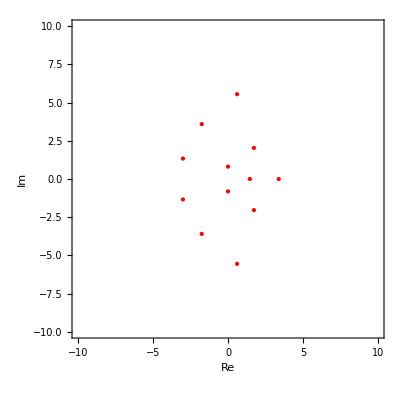

```mathematica
a=CoefficientList[Series[Exp[z  ϵ+  ϵ^2 +   ϵ^4 + ϵ^5 +   ϵ^7  +  ϵ^8 +  ϵ^10],{ϵ,0,10}],ϵ];
aa=Part[a,{1,2,3,4,5,6,7,8,9,10}];
aa[[0]]=0;
q =Wronskian[({aa[[2]],aa[[5]],aa[[8]]}),z]//FullSimplify;
s = Solve[q == 0,z];

rt = Flatten[Values[s]]
ComplexListPlot[rt,PlotRange->{{-10,10},{-10,10}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Red,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}]
```

{Root-5.05+3.34 ⅈRoot[{1+#1^2&,-2329600-537600 #1+1075200 #2+716800 #1 #2-358400 #2^2+179200 #1 #2^2-179200 #2^3+358400 #1 #2^3+89600 #1 #2^4-53760 #1 #2^5-4480 #2^6+8960 #1 #2^6-960 #2^7-2880 #1 #2^7+280 #2^8+1080 #1 #2^8+28 #2^10+28 #1 #2^10+#2^12&},{2,1}]-5.048441385405165,Root-2.25+0.398 ⅈRoot[{1+#1^2&,-2329600-537600 #1+1075200 #2+716800 #1 #2-358400 #2^2+179200 #1 #2^2-179200 #2^3+358400 #1 #2^3+89600 #1 #2^4-53760 #1 #2^5-4480 #2^6+8960 #1 #2^6-960 #2^7-2880 #1 #2^7+280 #2^8+1080 #1 #2^8+28 #2^10+28 #1 #2^10+#2^12&},{2,2}]-2.2452090904319166,Root-2.06-4.62 ⅈRoot[{1+#1^2&,-2329600-537600 #1+1075200 #2+716800 #1 #2-358400 #2^2+179200 #1 #2^2-179200 #2^3+358400 #1 #2^3+89600 #1 #2^4-53760 #1 #2^5-4480 #2^6+8960 #1 #2^6-960 #2^7-2880 #1 #2^7+280 #2^8+1080 #1 #2^8+28 #2^10+28 #1 #2^10+#2^12&},{2,3}]-2.0594419226134937,Root-1.85+4.32 ⅈRoot[{1+#1^2&,-2329600-537600 #1+1075200 #2+716800 #1 #2-358400 #2^2+179200 #1 #2^2-179200 #2^3+358400 #1 #2^3+89600 #1 #2^4-53760 #1 #2^5-4480 #2^6+8960 #1 #2^6-960 #2^7-2880 #1 #2^7+280 #2^8+1080 #1 #2^8+28 #2^10+28 #1 #2^10+#2^12&},{2,4}]-1.8511282300606204,Root-1.26-1.86 ⅈRoot[{1+#1^2&,-2329600-537600 #1+1075200 #2+716800 #1 #2-358400 #2^2+179200 #1 #2^2-179200 #2^3+358400 #1 #2^3+89600 #1 #2^4-53760 #1 #2^5-4480 #2^6+8960 #1 #2^6-960 #2^7-2880 #1 #2^7+280 #2^8+1080 #1 #2^8+28 #2^10+28 #1 #2^10+#2^12&},{2,5}]-1.260103303030136,Root0.160-4.04 ⅈRoot[{1+#1^2&,-2329600-537600 #1+1075200 #2+716800 #1 #2-358400 #2^2+179200 #1 #2^2-179200 #2^3+358400 #1 #2^3+89600 #1 #2^4-53760 #1 #2^5-4480 #2^6+8960 #1 #2^6-960 #2^7-2880 #1 #2^7+280 #2^8+1080 #1 #2^8+28 #2^10+28 #1 #2^10+#2^12&},{2,6}]0.15965931534599737,Root0.365+1.60 ⅈRoot[{1+#1^2&,-2329600-537600 #1+1075200 #2+716800 #1 #2-358400 #2^2+179200 #1 #2^2-179200 #2^3+358400 #1 #2^3+89600 #1 #2^4-53760 #1 #2^5-4480 #2^6+8960 #1 #2^6-960 #2^7-2880 #1 #2^7+280 #2^8+1080 #1 #2^8+28 #2^10+28 #1 #2^10+#2^12&},{2,7}]0.36488516708316965,Root0.782+5.68 ⅈRoot[{1+#1^2&,-2329600-537600 #1+1075200 #2+716800 #1 #2-358400 #2^2+179200 #1 #2^2-179200 #2^3+358400 #1 #2^3+89600 #1 #2^4-53760 #1 #2^5-4480 #2^6+8960 #1 #2^6-960 #2^7-2880 #1 #2^7+280 #2^8+1080 #1 #2^8+28 #2^10+28 #1 #2^10+#2^12&},{2,8}]0.7822393113978073,Root0.947-0.688 ⅈRoot[{1+#1^2&,-2329600-537600 #1+1075200 #2+716800 #1 #2-358400 #2^2+179200 #1 #2^2-179200 #2^3+358400 #1 #2^3+89600 #1 #2^4-53760 #1 #2^5-4480 #2^6+8960 #1 #2^6-960 #2^7-2880 #1 #2^7+280 #2^8+1080 #1 #2^8+28 #2^10+28 #1 #2^10+#2^12&},{2,9}]0.9473010937371026,Root2.66+1.64 ⅈRoot[{1+#1^2&,-2329600-537600 #1+1075200 #2+716800 #1 #2-358400 #2^2+179200 #1 #2^2-179200 #2^3+358400 #1 #2^3+89600 #1 #2^4-53760 #1 #2^5-4480 #2^6+8960 #1 #2^6-960 #2^7-2880 #1 #2^7+280 #2^8+1080 #1 #2^8+28 #2^10+28 #1 #2^10+#2^12&},{2,10}]2.66060534229046,Root3.67-0.955 ⅈRoot[{1+#1^2&,-2329600-537600 #1+1075200 #2+716800 #1 #2-358400 #2^2+179200 #1 #2^2-179200 #2^3+358400 #1 #2^3+89600 #1 #2^4-53760 #1 #2^5-4480 #2^6+8960 #1 #2^6-960 #2^7-2880 #1 #2^7+280 #2^8+1080 #1 #2^8+28 #2^10+28 #1 #2^10+#2^12&},{2,11}]3.666587510231907,Root3.88-4.82 ⅈRoot[{1+#1^2&,-2329600-537600 #1+1075200 #2+716800 #1 #2-358400 #2^2+179200 #1 #2^2-179200 #2^3+358400 #1 #2^3+89600 #1 #2^4-53760 #1 #2^5-4480 #2^6+8960 #1 #2^6-960 #2^7-2880 #1 #2^7+280 #2^8+1080 #1 #2^8+28 #2^10+28 #1 #2^10+#2^12&},{2,12}]3.8830461914548886}

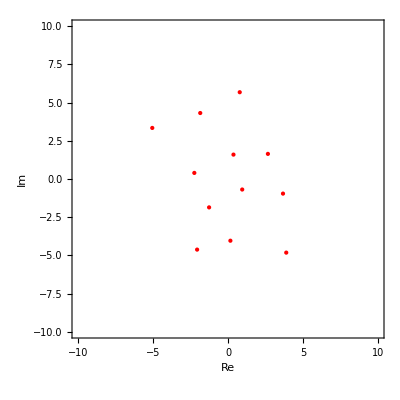

```mathematica
a=CoefficientList[Series[Exp[z  ϵ+(1+ⅈ)ϵ^2 -(1+2 ⅈ)  ϵ^4 + (1+3 ⅈ)ϵ^5 -(1+4 ⅈ)  ϵ^7  +  (1+5 ⅈ)ϵ^8 - (1+6ⅈ) ϵ^10],{ϵ,0,10}],ϵ];
aa=Part[a,{1,2,3,4,5,6,7,8,9,10}];
aa[[0]]=0;
q =Wronskian[({aa[[2]],aa[[5]],aa[[8]]}),z]//FullSimplify;
s = Solve[q == 0,z];

rt = Flatten[Values[s]]
ComplexListPlot[rt,PlotRange->{{-10,10},{-10,10}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Red,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}]
```

{Root-4.15+3.71 ⅈRoot[{1+#1^2&,-268800+537600 #1+358400 #2-134400 #2^2+224000 #1 #2^2+89600 #2^3+89600 #1 #2^3-11200 #2^4+22400 #1 #2^4-8960 #2^5-17920 #1 #2^5-2240 #2^6+6720 #1 #2^6-960 #2^7-960 #1 #2^7+280 #2^8+800 #1 #2^8+28 #2^10+28 #1 #2^10+#2^12&},{2,1}]-4.153908944108784,Root-2.25+0.918 ⅈRoot[{1+#1^2&,-268800+537600 #1+358400 #2-134400 #2^2+224000 #1 #2^2+89600 #2^3+89600 #1 #2^3-11200 #2^4+22400 #1 #2^4-8960 #2^5-17920 #1 #2^5-2240 #2^6+6720 #1 #2^6-960 #2^7-960 #1 #2^7+280 #2^8+800 #1 #2^8+28 #2^10+28 #1 #2^10+#2^12&},{2,2}]-2.2467100523618964,Root-1.73-3.70 ⅈRoot[{1+#1^2&,-268800+537600 #1+358400 #2-134400 #2^2+224000 #1 #2^2+89600 #2^3+89600 #1 #2^3-11200 #2^4+22400 #1 #2^4-8960 #2^5-17920 #1 #2^5-2240 #2^6+6720 #1 #2^6-960 #2^7-960 #1 #2^7+280 #2^8+800 #1 #2^8+28 #2^10+28 #1 #2^10+#2^12&},{2,3}]-1.7260979371529401,Root-1.29+3.97 ⅈRoot[{1+#1^2&,-268800+537600 #1+358400 #2-134400 #2^2+224000 #1 #2^2+89600 #2^3+89600 #1 #2^3-11200 #2^4+22400 #1 #2^4-8960 #2^5-17920 #1 #2^5-2240 #2^6+6720 #1 #2^6-960 #2^7-960 #1 #2^7+280 #2^8+800 #1 #2^8+28 #2^10+28 #1 #2^10+#2^12&},{2,4}]-1.2865483136243536,Root-0.932-1.54 ⅈRoot[{1+#1^2&,-268800+537600 #1+358400 #2-134400 #2^2+224000 #1 #2^2+89600 #2^3+89600 #1 #2^3-11200 #2^4+22400 #1 #2^4-8960 #2^5-17920 #1 #2^5-2240 #2^6+6720 #1 #2^6-960 #2^7-960 #1 #2^7+280 #2^8+800 #1 #2^8+28 #2^10+28 #1 #2^10+#2^12&},{2,5}]-0.9324442338765715,Root0.0360-3.65 ⅈRoot[{1+#1^2&,-268800+537600 #1+358400 #2-134400 #2^2+224000 #1 #2^2+89600 #2^3+89600 #1 #2^3-11200 #2^4+22400 #1 #2^4-8960 #2^5-17920 #1 #2^5-2240 #2^6+6720 #1 #2^6-960 #2^7-960 #1 #2^7+280 #2^8+800 #1 #2^8+28 #2^10+28 #1 #2^10+#2^12&},{2,6}]0.035993128947826726,Root0.311+1.46 ⅈRoot[{1+#1^2&,-268800+537600 #1+358400 #2-134400 #2^2+224000 #1 #2^2+89600 #2^3+89600 #1 #2^3-11200 #2^4+22400 #1 #2^4-8960 #2^5-17920 #1 #2^5-2240 #2^6+6720 #1 #2^6-960 #2^7-960 #1 #2^7+280 #2^8+800 #1 #2^8+28 #2^10+28 #1 #2^10+#2^12&},{2,7}]0.3113609801941037,Root0.418-1.01 ⅈRoot[{1+#1^2&,-268800+537600 #1+358400 #2-134400 #2^2+224000 #1 #2^2+89600 #2^3+89600 #1 #2^3-11200 #2^4+22400 #1 #2^4-8960 #2^5-17920 #1 #2^5-2240 #2^6+6720 #1 #2^6-960 #2^7-960 #1 #2^7+280 #2^8+800 #1 #2^8+28 #2^10+28 #1 #2^10+#2^12&},{2,8}]0.41769626260636533,Root0.862+4.80 ⅈRoot[{1+#1^2&,-268800+537600 #1+358400 #2-134400 #2^2+224000 #1 #2^2+89600 #2^3+89600 #1 #2^3-11200 #2^4+22400 #1 #2^4-8960 #2^5-17920 #1 #2^5-2240 #2^6+6720 #1 #2^6-960 #2^7-960 #1 #2^7+280 #2^8+800 #1 #2^8+28 #2^10+28 #1 #2^10+#2^12&},{2,9}]0.8623886889934808,Root2.23+1.12 ⅈRoot[{1+#1^2&,-268800+537600 #1+358400 #2-134400 #2^2+224000 #1 #2^2+89600 #2^3+89600 #1 #2^3-11200 #2^4+22400 #1 #2^4-8960 #2^5-17920 #1 #2^5-2240 #2^6+6720 #1 #2^6-960 #2^7-960 #1 #2^7+280 #2^8+800 #1 #2^8+28 #2^10+28 #1 #2^10+#2^12&},{2,10}]2.2284619082059316,Root3.21-1.42 ⅈRoot[{1+#1^2&,-268800+537600 #1+358400 #2-134400 #2^2+224000 #1 #2^2+89600 #2^3+89600 #1 #2^3-11200 #2^4+22400 #1 #2^4-8960 #2^5-17920 #1 #2^5-2240 #2^6+6720 #1 #2^6-960 #2^7-960 #1 #2^7+280 #2^8+800 #1 #2^8+28 #2^10+28 #1 #2^10+#2^12&},{2,11}]3.2144374636150506,Root3.28-4.65 ⅈRoot[{1+#1^2&,-268800+537600 #1+358400 #2-134400 #2^2+224000 #1 #2^2+89600 #2^3+89600 #1 #2^3-11200 #2^4+22400 #1 #2^4-8960 #2^5-17920 #1 #2^5-2240 #2^6+6720 #1 #2^6-960 #2^7-960 #1 #2^7+280 #2^8+800 #1 #2^8+28 #2^10+28 #1 #2^10+#2^12&},{2,12}]3.275371048561787}

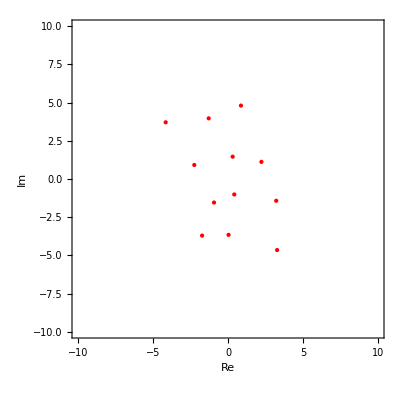

```mathematica
a=CoefficientList[Series[Exp[z  ϵ+(1+ⅈ)ϵ^2 -(1+ⅈ)  ϵ^4 +(1+ⅈ)ϵ^5 -(1+ⅈ)  ϵ^7  + (1+ⅈ)ϵ^8 - (1+ⅈ) ϵ^10],{ϵ,0,10}],ϵ];
aa=Part[a,{1,2,3,4,5,6,7,8,9,10}];
aa[[0]]=0;
q =Wronskian[({aa[[2]],aa[[5]],aa[[8]]}),z]//FullSimplify;
s = Solve[q == 0,z];

rt = Flatten[Values[s]]
ComplexListPlot[rt,PlotRange->{{-10,10},{-10,10}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Red,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}]
```

{Root-3.51+0.940 ⅈRoot[{1+#1^2&,-448000-358400 #1+358400 #2-492800 #2^2+224000 #1 #2^2+89600 #2^3-268800 #1 #2^3+33600 #2^4-22400 #1 #2^4+8960 #2^5-2240 #2^6-2240 #1 #2^6-960 #2^7-960 #1 #2^7-280 #2^8+240 #1 #2^8+28 #2^10+28 #1 #2^10+#2^12&},{2,1}]-3.513247066119302,Root-2.81+3.50 ⅈRoot[{1+#1^2&,-448000-358400 #1+358400 #2-492800 #2^2+224000 #1 #2^2+89600 #2^3-268800 #1 #2^3+33600 #2^4-22400 #1 #2^4+8960 #2^5-2240 #2^6-2240 #1 #2^6-960 #2^7-960 #1 #2^7-280 #2^8+240 #1 #2^8+28 #2^10+28 #1 #2^10+#2^12&},{2,2}]-2.8094262054492125,Root-2.72-1.85 ⅈRoot[{1+#1^2&,-448000-358400 #1+358400 #2-492800 #2^2+224000 #1 #2^2+89600 #2^3-268800 #1 #2^3+33600 #2^4-22400 #1 #2^4+8960 #2^5-2240 #2^6-2240 #1 #2^6-960 #2^7-960 #1 #2^7-280 #2^8+240 #1 #2^8+28 #2^10+28 #1 #2^10+#2^12&},{2,3}]-2.7166069623975178,Root-0.997+5.78 ⅈRoot[{1+#1^2&,-448000-358400 #1+358400 #2-492800 #2^2+224000 #1 #2^2+89600 #2^3-268800 #1 #2^3+33600 #2^4-22400 #1 #2^4+8960 #2^5-2240 #2^6-2240 #1 #2^6-960 #2^7-960 #1 #2^7-280 #2^8+240 #1 #2^8+28 #2^10+28 #1 #2^10+#2^12&},{2,4}]-0.9968050080917339,Root-0.832-4.04 ⅈRoot[{1+#1^2&,-448000-358400 #1+358400 #2-492800 #2^2+224000 #1 #2^2+89600 #2^3-268800 #1 #2^3+33600 #2^4-22400 #1 #2^4+8960 #2^5-2240 #2^6-2240 #1 #2^6-960 #2^7-960 #1 #2^7-280 #2^8+240 #1 #2^8+28 #2^10+28 #1 #2^10+#2^12&},{2,5}]-0.832173010797397,Root-0.508+0.968 ⅈRoot[{1+#1^2&,-448000-358400 #1+358400 #2-492800 #2^2+224000 #1 #2^2+89600 #2^3-268800 #1 #2^3+33600 #2^4-22400 #1 #2^4+8960 #2^5-2240 #2^6-2240 #1 #2^6-960 #2^7-960 #1 #2^7-280 #2^8+240 #1 #2^8+28 #2^10+28 #1 #2^10+#2^12&},{2,6}]-0.5077370440499314,Root0.391+2.62 ⅈRoot[{1+#1^2&,-448000-358400 #1+358400 #2-492800 #2^2+224000 #1 #2^2+89600 #2^3-268800 #1 #2^3+33600 #2^4-22400 #1 #2^4+8960 #2^5-2240 #2^6-2240 #1 #2^6-960 #2^7-960 #1 #2^7-280 #2^8+240 #1 #2^8+28 #2^10+28 #1 #2^10+#2^12&},{2,7}]0.3911187530732751,Root0.552-0.831 ⅈRoot[{1+#1^2&,-448000-358400 #1+358400 #2-492800 #2^2+224000 #1 #2^2+89600 #2^3-268800 #1 #2^3+33600 #2^4-22400 #1 #2^4+8960 #2^5-2240 #2^6-2240 #1 #2^6-960 #2^7-960 #1 #2^7-280 #2^8+240 #1 #2^8+28 #2^10+28 #1 #2^10+#2^12&},{2,8}]0.5520353963523023,Root1.40+0.882 ⅈRoot[{1+#1^2&,-448000-358400 #1+358400 #2-492800 #2^2+224000 #1 #2^2+89600 #2^3-268800 #1 #2^3+33600 #2^4-22400 #1 #2^4+8960 #2^5-2240 #2^6-2240 #1 #2^6-960 #2^7-960 #1 #2^7-280 #2^8+240 #1 #2^8+28 #2^10+28 #1 #2^10+#2^12&},{2,9}]1.396560053325861,Root2.16-5.99 ⅈRoot[{1+#1^2&,-448000-358400 #1+358400 #2-492800 #2^2+224000 #1 #2^2+89600 #2^3-268800 #1 #2^3+33600 #2^4-22400 #1 #2^4+8960 #2^5-2240 #2^6-2240 #1 #2^6-960 #2^7-960 #1 #2^7-280 #2^8+240 #1 #2^8+28 #2^10+28 #1 #2^10+#2^12&},{2,10}]2.162103163960733,Root3.05-2.26 ⅈRoot[{1+#1^2&,-448000-358400 #1+358400 #2-492800 #2^2+224000 #1 #2^2+89600 #2^3-268800 #1 #2^3+33600 #2^4-22400 #1 #2^4+8960 #2^5-2240 #2^6-2240 #1 #2^6-960 #2^7-960 #1 #2^7-280 #2^8+240 #1 #2^8+28 #2^10+28 #1 #2^10+#2^12&},{2,11}]3.0506604688661207,Root3.82+0.274 ⅈRoot[{1+#1^2&,-448000-358400 #1+358400 #2-492800 #2^2+224000 #1 #2^2+89600 #2^3-268800 #1 #2^3+33600 #2^4-22400 #1 #2^4+8960 #2^5-2240 #2^6-2240 #1 #2^6-960 #2^7-960 #1 #2^7-280 #2^8+240 #1 #2^8+28 #2^10+28 #1 #2^10+#2^12&},{2,12}]3.823517461326802}

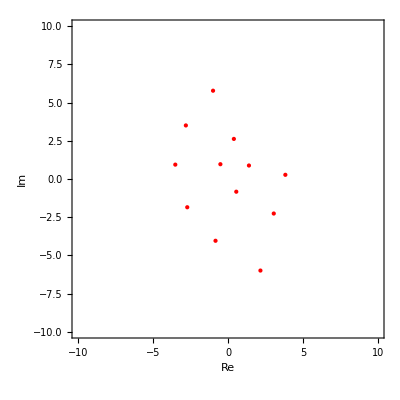

```mathematica
a=CoefficientList[Series[Exp[z  ϵ+(1+ⅈ)ϵ^2+(1+ⅈ)  ϵ^4 +(1+ⅈ)ϵ^5 +(1+ⅈ)  ϵ^7  + (1+ⅈ)ϵ^8 +(1+ⅈ) ϵ^10],{ϵ,0,10}],ϵ];
aa=Part[a,{1,2,3,4,5,6,7,8,9,10}];
aa[[0]]=0;
q =Wronskian[({aa[[2]],aa[[5]],aa[[8]]}),z]//FullSimplify;
s = Solve[q == 0,z];

rt = Flatten[Values[s]]
ComplexListPlot[rt,PlotRange->{{-10,10},{-10,10}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Red,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}]
```

{Root-2.70Root[1120-5040 #1+2240 #1^2-280 #1^4-56 #1^5+16 #1^7+#1^9&,1]-2.6974493903138073,Root0.250Root[1120-5040 #1+2240 #1^2-280 #1^4-56 #1^5+16 #1^7+#1^9&,2]0.24970870702864786,Root2.52Root[1120-5040 #1+2240 #1^2-280 #1^4-56 #1^5+16 #1^7+#1^9&,3]2.515766393410886,Root-1.79-2.48 ⅈRoot[1120-5040 #1+2240 #1^2-280 #1^4-56 #1^5+16 #1^7+#1^9&,4]-1.790037527891566,Root-1.79+2.48 ⅈRoot[1120-5040 #1+2240 #1^2-280 #1^4-56 #1^5+16 #1^7+#1^9&,5]-1.790037527891566,Root0.361-4.52 ⅈRoot[1120-5040 #1+2240 #1^2-280 #1^4-56 #1^5+16 #1^7+#1^9&,6]0.360592027959151,Root0.361+4.52 ⅈRoot[1120-5040 #1+2240 #1^2-280 #1^4-56 #1^5+16 #1^7+#1^9&,7]0.360592027959151,Root1.40-1.21 ⅈRoot[1120-5040 #1+2240 #1^2-280 #1^4-56 #1^5+16 #1^7+#1^9&,8]1.395432644869552,Root1.40+1.21 ⅈRoot[1120-5040 #1+2240 #1^2-280 #1^4-56 #1^5+16 #1^7+#1^9&,9]1.395432644869552}

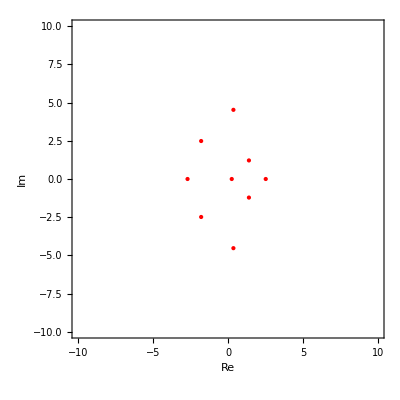

```mathematica
a=CoefficientList[Series[Exp[z  ϵ+ϵ^2 + ϵ^4 +ϵ^5 +ϵ^7  + ((5ⅈ)/11)ϵ^8 +((5ⅈ)/13)ϵ^10],{ϵ,0,10}],ϵ];
aa=Part[a,{1,2,3,4,5,6,7,8,9,10}];
aa[[0]]=0;
q =Wronskian[({aa[[2]],aa[[5]],aa[[8]]}),z]//FullSimplify;
s = Solve[q == 0,z];

rt = Flatten[Values[s]]
ComplexListPlot[rt,PlotRange->{{-10,10},{-10,10}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Red,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}]
```

{Root-5.22+3.88 ⅈRoot[{1+#1^4-#1^20-#1^24-#1^28-#1^32+#1^40+#1^44+#1^48+#1^52+#1^56-#1^64-#1^68-#1^72-#1^76+#1^92+#1^96&,1+#2^2&,-22400 #1^28+44800 #1^63-31360 #1^90-8960 #3-35840 #1^35 #3-35840 #2 #3-11200 #1^2 #3^2-11200 #1^6 #3^2-7840 #1^20 #3^2+11200 #1^22 #3^2+11200 #1^26 #3^2+11200 #1^30 #3^2+11200 #1^34 #3^2-11200 #1^42 #3^2-11200 #1^46 #3^2-11200 #1^50 #3^2-11200 #1^54 #3^2-11200 #1^58 #3^2+11200 #1^66 #3^2+11200 #1^70 #3^2+11200 #1^74 #3^2+11200 #1^78 #3^2-11200 #1^94 #3^2-1400 #1^28 #3^4-224 #3^5+448 #1^35 #3^5+32 #2 #3^7+#3^9&},{96,2,1}]-5.215136887110341,Root-2.90-0.458 ⅈRoot[{1+#1^4-#1^20-#1^24-#1^28-#1^32+#1^40+#1^44+#1^48+#1^52+#1^56-#1^64-#1^68-#1^72-#1^76+#1^92+#1^96&,1+#2^2&,-22400 #1^28+44800 #1^63-31360 #1^90-8960 #3-35840 #1^35 #3-35840 #2 #3-11200 #1^2 #3^2-11200 #1^6 #3^2-7840 #1^20 #3^2+11200 #1^22 #3^2+11200 #1^26 #3^2+11200 #1^30 #3^2+11200 #1^34 #3^2-11200 #1^42 #3^2-11200 #1^46 #3^2-11200 #1^50 #3^2-11200 #1^54 #3^2-11200 #1^58 #3^2+11200 #1^66 #3^2+11200 #1^70 #3^2+11200 #1^74 #3^2+11200 #1^78 #3^2-11200 #1^94 #3^2-1400 #1^28 #3^4-224 #3^5+448 #1^35 #3^5+32 #2 #3^7+#3^9&},{96,2,2}]-2.9017520223492514,Root-2.01-3.12 ⅈRoot[{1+#1^4-#1^20-#1^24-#1^28-#1^32+#1^40+#1^44+#1^48+#1^52+#1^56-#1^64-#1^68-#1^72-#1^76+#1^92+#1^96&,1+#2^2&,-22400 #1^28+44800 #1^63-31360 #1^90-8960 #3-35840 #1^35 #3-35840 #2 #3-11200 #1^2 #3^2-11200 #1^6 #3^2-7840 #1^20 #3^2+11200 #1^22 #3^2+11200 #1^26 #3^2+11200 #1^30 #3^2+11200 #1^34 #3^2-11200 #1^42 #3^2-11200 #1^46 #3^2-11200 #1^50 #3^2-11200 #1^54 #3^2-11200 #1^58 #3^2+11200 #1^66 #3^2+11200 #1^70 #3^2+11200 #1^74 #3^2+11200 #1^78 #3^2-11200 #1^94 #3^2-1400 #1^28 #3^4-224 #3^5+448 #1^35 #3^5+32 #2 #3^7+#3^9&},{96,2,3}]-2.01491832296382,Root-0.605+4.14 ⅈRoot[{1+#1^4-#1^20-#1^24-#1^28-#1^32+#1^40+#1^44+#1^48+#1^52+#1^56-#1^64-#1^68-#1^72-#1^76+#1^92+#1^96&,1+#2^2&,-22400 #1^28+44800 #1^63-31360 #1^90-8960 #3-35840 #1^35 #3-35840 #2 #3-11200 #1^2 #3^2-11200 #1^6 #3^2-7840 #1^20 #3^2+11200 #1^22 #3^2+11200 #1^26 #3^2+11200 #1^30 #3^2+11200 #1^34 #3^2-11200 #1^42 #3^2-11200 #1^46 #3^2-11200 #1^50 #3^2-11200 #1^54 #3^2-11200 #1^58 #3^2+11200 #1^66 #3^2+11200 #1^70 #3^2+11200 #1^74 #3^2+11200 #1^78 #3^2-11200 #1^94 #3^2-1400 #1^28 #3^4-224 #3^5+448 #1^35 #3^5+32 #2 #3^7+#3^9&},{96,2,4}]-0.6053582506374574,Root0.0527-0.0107 ⅈRoot[{1+#1^4-#1^20-#1^24-#1^28-#1^32+#1^40+#1^44+#1^48+#1^52+#1^56-#1^64-#1^68-#1^72-#1^76+#1^92+#1^96&,1+#2^2&,-22400 #1^28+44800 #1^63-31360 #1^90-8960 #3-35840 #1^35 #3-35840 #2 #3-11200 #1^2 #3^2-11200 #1^6 #3^2-7840 #1^20 #3^2+11200 #1^22 #3^2+11200 #1^26 #3^2+11200 #1^30 #3^2+11200 #1^34 #3^2-11200 #1^42 #3^2-11200 #1^46 #3^2-11200 #1^50 #3^2-11200 #1^54 #3^2-11200 #1^58 #3^2+11200 #1^66 #3^2+11200 #1^70 #3^2+11200 #1^74 #3^2+11200 #1^78 #3^2-11200 #1^94 #3^2-1400 #1^28 #3^4-224 #3^5+448 #1^35 #3^5+32 #2 #3^7+#3^9&},{96,2,5}]0.0527139374116413,Root0.812-2.75 ⅈRoot[{1+#1^4-#1^20-#1^24-#1^28-#1^32+#1^40+#1^44+#1^48+#1^52+#1^56-#1^64-#1^68-#1^72-#1^76+#1^92+#1^96&,1+#2^2&,-22400 #1^28+44800 #1^63-31360 #1^90-8960 #3-35840 #1^35 #3-35840 #2 #3-11200 #1^2 #3^2-11200 #1^6 #3^2-7840 #1^20 #3^2+11200 #1^22 #3^2+11200 #1^26 #3^2+11200 #1^30 #3^2+11200 #1^34 #3^2-11200 #1^42 #3^2-11200 #1^46 #3^2-11200 #1^50 #3^2-11200 #1^54 #3^2-11200 #1^58 #3^2+11200 #1^66 #3^2+11200 #1^70 #3^2+11200 #1^74 #3^2+11200 #1^78 #3^2-11200 #1^94 #3^2-1400 #1^28 #3^4-224 #3^5+448 #1^35 #3^5+32 #2 #3^7+#3^9&},{96,2,6}]0.8118535970047038,Root1.79+3.13 ⅈRoot[{1+#1^4-#1^20-#1^24-#1^28-#1^32+#1^40+#1^44+#1^48+#1^52+#1^56-#1^64-#1^68-#1^72-#1^76+#1^92+#1^96&,1+#2^2&,-22400 #1^28+44800 #1^63-31360 #1^90-8960 #3-35840 #1^35 #3-35840 #2 #3-11200 #1^2 #3^2-11200 #1^6 #3^2-7840 #1^20 #3^2+11200 #1^22 #3^2+11200 #1^26 #3^2+11200 #1^30 #3^2+11200 #1^34 #3^2-11200 #1^42 #3^2-11200 #1^46 #3^2-11200 #1^50 #3^2-11200 #1^54 #3^2-11200 #1^58 #3^2+11200 #1^66 #3^2+11200 #1^70 #3^2+11200 #1^74 #3^2+11200 #1^78 #3^2-11200 #1^94 #3^2-1400 #1^28 #3^4-224 #3^5+448 #1^35 #3^5+32 #2 #3^7+#3^9&},{96,2,7}]1.7925842918322004,Root3.79-0.716 ⅈRoot[{1+#1^4-#1^20-#1^24-#1^28-#1^32+#1^40+#1^44+#1^48+#1^52+#1^56-#1^64-#1^68-#1^72-#1^76+#1^92+#1^96&,1+#2^2&,-22400 #1^28+44800 #1^63-31360 #1^90-8960 #3-35840 #1^35 #3-35840 #2 #3-11200 #1^2 #3^2-11200 #1^6 #3^2-7840 #1^20 #3^2+11200 #1^22 #3^2+11200 #1^26 #3^2+11200 #1^30 #3^2+11200 #1^34 #3^2-11200 #1^42 #3^2-11200 #1^46 #3^2-11200 #1^50 #3^2-11200 #1^54 #3^2-11200 #1^58 #3^2+11200 #1^66 #3^2+11200 #1^70 #3^2+11200 #1^74 #3^2+11200 #1^78 #3^2-11200 #1^94 #3^2-1400 #1^28 #3^4-224 #3^5+448 #1^35 #3^5+32 #2 #3^7+#3^9&},{96,2,8}]3.792095487871677,Root4.29-4.09 ⅈRoot[{1+#1^4-#1^20-#1^24-#1^28-#1^32+#1^40+#1^44+#1^48+#1^52+#1^56-#1^64-#1^68-#1^72-#1^76+#1^92+#1^96&,1+#2^2&,-22400 #1^28+44800 #1^63-31360 #1^90-8960 #3-35840 #1^35 #3-35840 #2 #3-11200 #1^2 #3^2-11200 #1^6 #3^2-7840 #1^20 #3^2+11200 #1^22 #3^2+11200 #1^26 #3^2+11200 #1^30 #3^2+11200 #1^34 #3^2-11200 #1^42 #3^2-11200 #1^46 #3^2-11200 #1^50 #3^2-11200 #1^54 #3^2-11200 #1^58 #3^2+11200 #1^66 #3^2+11200 #1^70 #3^2+11200 #1^74 #3^2+11200 #1^78 #3^2-11200 #1^94 #3^2-1400 #1^28 #3^4-224 #3^5+448 #1^35 #3^5+32 #2 #3^7+#3^9&},{96,2,9}]4.287918168940648}

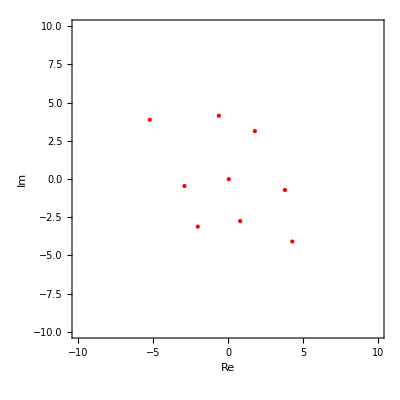

```mathematica
a=CoefficientList[Series[Exp[z  ϵ+2Exp[ⅈ 1/2 Pi] ϵ^2 -4Exp[ⅈ 1/4 Pi]ϵ^4 +5Exp[ⅈ 1/5 Pi]ϵ^5 -7Exp[ⅈ 1/7 Pi] ϵ^7  + (1+ⅈ)ϵ^8 - (1+ⅈ) ϵ^10],{ϵ,0,10}],ϵ];
aa=Part[a,{1,2,3,4,5,6,7,8,9,10}];
aa[[0]]=0;
q =Wronskian[({aa[[2]],aa[[5]],aa[[8]]}),z]//FullSimplify;
s = Solve[q == 0,z];

rt = Flatten[Values[s]]
ComplexListPlot[rt,PlotRange->{{-10,10},{-10,10}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Red,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}]
```

{Root-2.56Root[48 π^2+56 π^3+(-140 π^2-140 π^3-35 π^4) #1+(160 π+112 π^2) #1^2-56 π #1^4+(-28 π+14 π^2) #1^5+8 π #1^7+#1^9&,1]-2.5630321897812056,Root0.253Root[48 π^2+56 π^3+(-140 π^2-140 π^3-35 π^4) #1+(160 π+112 π^2) #1^2-56 π #1^4+(-28 π+14 π^2) #1^5+8 π #1^7+#1^9&,2]0.2532370147648211,Root2.35Root[48 π^2+56 π^3+(-140 π^2-140 π^3-35 π^4) #1+(160 π+112 π^2) #1^2-56 π #1^4+(-28 π+14 π^2) #1^5+8 π #1^7+#1^9&,3]2.350089259707576,Root-1.59-2.72 ⅈRoot[48 π^2+56 π^3+(-140 π^2-140 π^3-35 π^4) #1+(160 π+112 π^2) #1^2-56 π #1^4+(-28 π+14 π^2) #1^5+8 π #1^7+#1^9&,4]-1.5890782484830186,Root-1.59+2.72 ⅈRoot[48 π^2+56 π^3+(-140 π^2-140 π^3-35 π^4) #1+(160 π+112 π^2) #1^2-56 π #1^4+(-28 π+14 π^2) #1^5+8 π #1^7+#1^9&,5]-1.5890782484830186,Root0.205-4.90 ⅈRoot[48 π^2+56 π^3+(-140 π^2-140 π^3-35 π^4) #1+(160 π+112 π^2) #1^2-56 π #1^4+(-28 π+14 π^2) #1^5+8 π #1^7+#1^9&,6]0.2052951166979159,Root0.205+4.90 ⅈRoot[48 π^2+56 π^3+(-140 π^2-140 π^3-35 π^4) #1+(160 π+112 π^2) #1^2-56 π #1^4+(-28 π+14 π^2) #1^5+8 π #1^7+#1^9&,7]0.2052951166979159,Root1.36-2.05 ⅈRoot[48 π^2+56 π^3+(-140 π^2-140 π^3-35 π^4) #1+(160 π+112 π^2) #1^2-56 π #1^4+(-28 π+14 π^2) #1^5+8 π #1^7+#1^9&,8]1.3636360894395072,Root1.36+2.05 ⅈRoot[48 π^2+56 π^3+(-140 π^2-140 π^3-35 π^4) #1+(160 π+112 π^2) #1^2-56 π #1^4+(-28 π+14 π^2) #1^5+8 π #1^7+#1^9&,9]1.3636360894395072}

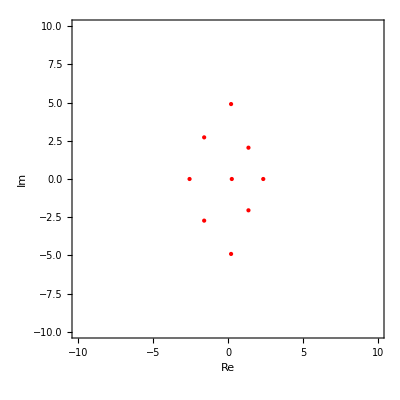

```mathematica
a=CoefficientList[Series[Exp[z  ϵ+1/2 Pi ϵ^2 +1/4 Pi ϵ^4 +1/5 Pi ϵ^5 +1/7 Pi ϵ^7  + (1+ⅈ)ϵ^8 - (1+ⅈ) ϵ^10],{ϵ,0,10}],ϵ];
aa=Part[a,{1,2,3,4,5,6,7,8,9,10}];
aa[[0]]=0;
q =Wronskian[({aa[[2]],aa[[5]],aa[[8]]}),z]//FullSimplify;
s = Solve[q == 0,z];

rt = Flatten[Values[s]]
ComplexListPlot[rt,PlotRange->{{-10,10},{-10,10}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Red,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}]
```

{Root-4.13Root[13547520-10160640 #1+2116800 #1^2-5503680 #1^3+1975680 #1^4+197568 #1^5+70560 #1^6-23184 #1^7+10080 #1^8-4704 #1^9-980 #1^10-308 #1^11+28 #1^13+#1^15&,1]-4.126789204393083,Root1.17Root[13547520-10160640 #1+2116800 #1^2-5503680 #1^3+1975680 #1^4+197568 #1^5+70560 #1^6-23184 #1^7+10080 #1^8-4704 #1^9-980 #1^10-308 #1^11+28 #1^13+#1^15&,2]1.1699311599266549,Root2.39Root[13547520-10160640 #1+2116800 #1^2-5503680 #1^3+1975680 #1^4+197568 #1^5+70560 #1^6-23184 #1^7+10080 #1^8-4704 #1^9-980 #1^10-308 #1^11+28 #1^13+#1^15&,3]2.3860913800355266,Root2.66Root[13547520-10160640 #1+2116800 #1^2-5503680 #1^3+1975680 #1^4+197568 #1^5+70560 #1^6-23184 #1^7+10080 #1^8-4704 #1^9-980 #1^10-308 #1^11+28 #1^13+#1^15&,4]2.6589423990675916,Root3.81Root[13547520-10160640 #1+2116800 #1^2-5503680 #1^3+1975680 #1^4+197568 #1^5+70560 #1^6-23184 #1^7+10080 #1^8-4704 #1^9-980 #1^10-308 #1^11+28 #1^13+#1^15&,5]3.808788607649856,Root-2.56-1.85 ⅈRoot[13547520-10160640 #1+2116800 #1^2-5503680 #1^3+1975680 #1^4+197568 #1^5+70560 #1^6-23184 #1^7+10080 #1^8-4704 #1^9-980 #1^10-308 #1^11+28 #1^13+#1^15&,6]-2.557931706158677,Root-2.56+1.85 ⅈRoot[13547520-10160640 #1+2116800 #1^2-5503680 #1^3+1975680 #1^4+197568 #1^5+70560 #1^6-23184 #1^7+10080 #1^8-4704 #1^9-980 #1^10-308 #1^11+28 #1^13+#1^15&,7]-2.557931706158677,Root-1.55-3.53 ⅈRoot[13547520-10160640 #1+2116800 #1^2-5503680 #1^3+1975680 #1^4+197568 #1^5+70560 #1^6-23184 #1^7+10080 #1^8-4704 #1^9-980 #1^10-308 #1^11+28 #1^13+#1^15&,8]-1.552549936128548,Root-1.55+3.53 ⅈRoot[13547520-10160640 #1+2116800 #1^2-5503680 #1^3+1975680 #1^4+197568 #1^5+70560 #1^6-23184 #1^7+10080 #1^8-4704 #1^9-980 #1^10-308 #1^11+28 #1^13+#1^15&,9]-1.552549936128548,Root-0.505-1.39 ⅈRoot[13547520-10160640 #1+2116800 #1^2-5503680 #1^3+1975680 #1^4+197568 #1^5+70560 #1^6-23184 #1^7+10080 #1^8-4704 #1^9-980 #1^10-308 #1^11+28 #1^13+#1^15&,10]-0.5054721074998229,Root-0.505+1.39 ⅈRoot[13547520-10160640 #1+2116800 #1^2-5503680 #1^3+1975680 #1^4+197568 #1^5+70560 #1^6-23184 #1^7+10080 #1^8-4704 #1^9-980 #1^10-308 #1^11+28 #1^13+#1^15&,11]-0.5054721074998229,Root0.435-5.94 ⅈRoot[13547520-10160640 #1+2116800 #1^2-5503680 #1^3+1975680 #1^4+197568 #1^5+70560 #1^6-23184 #1^7+10080 #1^8-4704 #1^9-980 #1^10-308 #1^11+28 #1^13+#1^15&,12]0.43474140352035945,Root0.435+5.94 ⅈRoot[13547520-10160640 #1+2116800 #1^2-5503680 #1^3+1975680 #1^4+197568 #1^5+70560 #1^6-23184 #1^7+10080 #1^8-4704 #1^9-980 #1^10-308 #1^11+28 #1^13+#1^15&,13]0.43474140352035945,Root1.23-2.94 ⅈRoot[13547520-10160640 #1+2116800 #1^2-5503680 #1^3+1975680 #1^4+197568 #1^5+70560 #1^6-23184 #1^7+10080 #1^8-4704 #1^9-980 #1^10-308 #1^11+28 #1^13+#1^15&,14]1.2327301751234152,Root1.23+2.94 ⅈRoot[13547520-10160640 #1+2116800 #1^2-5503680 #1^3+1975680 #1^4+197568 #1^5+70560 #1^6-23184 #1^7+10080 #1^8-4704 #1^9-980 #1^10-308 #1^11+28 #1^13+#1^15&,15]1.2327301751234152}

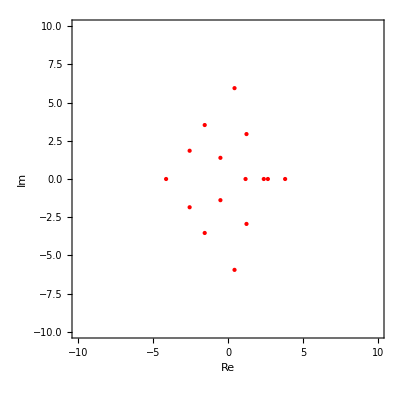

```mathematica
a=CoefficientList[Series[Exp[z  ϵ+ϵ^2 +ϵ^4 + ϵ^5 +ϵ^7  + ϵ^8 +ϵ^10+ϵ^11+ϵ^13],{ϵ,0,10}],ϵ];
aa=Part[a,{1,2,3,4,5,6,7,8,9,10}];
aa[[0]]=0;
q =Wronskian[({aa[[2]],aa[[5]],aa[[8]],aa[[10]]}),z]//FullSimplify;
s = Solve[q == 0,z];

rt = Flatten[Values[s]]
ComplexListPlot[rt,PlotRange->{{-10,10},{-10,10}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Red,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}]
```

{0,0,0,Root-4.65-1.93 ⅈRoot[{1+#1^2&,3386880 #1+12096 #2^4-616 #1 #2^8+#2^12&},{2,1}]-4.652310198700275,Root-2.92+0.136 ⅈRoot[{1+#1^2&,3386880 #1+12096 #2^4-616 #1 #2^8+#2^12&},{2,2}]-2.9155662747774933,Root-2.16+1.97 ⅈRoot[{1+#1^2&,3386880 #1+12096 #2^4-616 #1 #2^8+#2^12&},{2,3}]-2.158132320854359,Root-1.97-2.16 ⅈRoot[{1+#1^2&,3386880 #1+12096 #2^4-616 #1 #2^8+#2^12&},{2,4}]-1.9651010469335741,Root-1.93+4.65 ⅈRoot[{1+#1^2&,3386880 #1+12096 #2^4-616 #1 #2^8+#2^12&},{2,5}]-1.9270499806683226,Root-0.136-2.92 ⅈRoot[{1+#1^2&,3386880 #1+12096 #2^4-616 #1 #2^8+#2^12&},{2,6}]-0.13649372277046481,Root0.136+2.92 ⅈRoot[{1+#1^2&,3386880 #1+12096 #2^4-616 #1 #2^8+#2^12&},{2,7}]0.13649372277046481,Root1.93-4.65 ⅈRoot[{1+#1^2&,3386880 #1+12096 #2^4-616 #1 #2^8+#2^12&},{2,8}]1.9270499806683226,Root1.97+2.16 ⅈRoot[{1+#1^2&,3386880 #1+12096 #2^4-616 #1 #2^8+#2^12&},{2,9}]1.9651010469335741,Root2.16-1.97 ⅈRoot[{1+#1^2&,3386880 #1+12096 #2^4-616 #1 #2^8+#2^12&},{2,10}]2.158132320854359,Root2.92-0.136 ⅈRoot[{1+#1^2&,3386880 #1+12096 #2^4-616 #1 #2^8+#2^12&},{2,11}]2.9155662747774933,Root4.65+1.93 ⅈRoot[{1+#1^2&,3386880 #1+12096 #2^4-616 #1 #2^8+#2^12&},{2,12}]4.652310198700275}

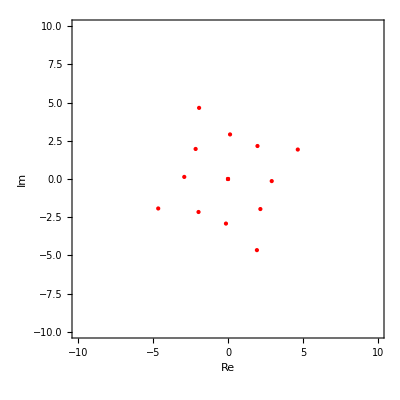

```mathematica
a=CoefficientList[Series[Exp[z  ϵ +ⅈ ϵ^4    +ⅈ ϵ^8 +ⅈ ϵ^10+ⅈ ϵ^11+ⅈ ϵ^13],{ϵ,0,10}],ϵ];
aa=Part[a,{1,2,3,4,5,6,7,8,9,10}];
aa[[0]]=0;
q =Wronskian[({aa[[2]],aa[[5]],aa[[8]],aa[[10]]}),z]//FullSimplify;
s = Solve[q == 0,z];

rt = Flatten[Values[s]]
ComplexListPlot[rt,PlotRange->{{-10,10},{-10,10}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Red,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}]
```

{Root-2.74+1.51 ⅈRoot[{1+#1^2&,-1120 #1+1680 #2+2240 #1 #2-1120 #2^2+1120 #1 #2^2-280 #1 #2^4-56 #2^5-112 #1 #2^5+16 #1 #2^7+#2^9&},{2,1}]-2.7434190851017353,Root-2.41-0.746 ⅈRoot[{1+#1^2&,-1120 #1+1680 #2+2240 #1 #2-1120 #2^2+1120 #1 #2^2-280 #1 #2^4-56 #2^5-112 #1 #2^5+16 #1 #2^7+#2^9&},{2,2}]-2.410363490937923,Root-1.71+3.50 ⅈRoot[{1+#1^2&,-1120 #1+1680 #2+2240 #1 #2-1120 #2^2+1120 #1 #2^2-280 #1 #2^4-56 #2^5-112 #1 #2^5+16 #1 #2^7+#2^9&},{2,3}]-1.7138762043292037,Root-0.624-2.36 ⅈRoot[{1+#1^2&,-1120 #1+1680 #2+2240 #1 #2-1120 #2^2+1120 #1 #2^2-280 #1 #2^4-56 #2^5-112 #1 #2^5+16 #1 #2^7+#2^9&},{2,4}]-0.6242820766380841,Root-0.431+1.21 ⅈRoot[{1+#1^2&,-1120 #1+1680 #2+2240 #1 #2-1120 #2^2+1120 #1 #2^2-280 #1 #2^4-56 #2^5-112 #1 #2^5+16 #1 #2^7+#2^9&},{2,5}]-0.4308107123206048,Root0.380+0.167 ⅈRoot[{1+#1^2&,-1120 #1+1680 #2+2240 #1 #2-1120 #2^2+1120 #1 #2^2-280 #1 #2^4-56 #2^5-112 #1 #2^5+16 #1 #2^7+#2^9&},{2,6}]0.37959286292487837,Root2.03+0.466 ⅈRoot[{1+#1^2&,-1120 #1+1680 #2+2240 #1 #2-1120 #2^2+1120 #1 #2^2-280 #1 #2^4-56 #2^5-112 #1 #2^5+16 #1 #2^7+#2^9&},{2,7}]2.0263517030867026,Root2.56-3.75 ⅈRoot[{1+#1^2&,-1120 #1+1680 #2+2240 #1 #2-1120 #2^2+1120 #1 #2^2-280 #1 #2^4-56 #2^5-112 #1 #2^5+16 #1 #2^7+#2^9&},{2,8}]2.556170217123145,Root2.96-8.95 × 10^-3 ⅈRoot[{1+#1^2&,-1120 #1+1680 #2+2240 #1 #2-1120 #2^2+1120 #1 #2^2-280 #1 #2^4-56 #2^5-112 #1 #2^5+16 #1 #2^7+#2^9&},{2,9}]2.9606367861928247}

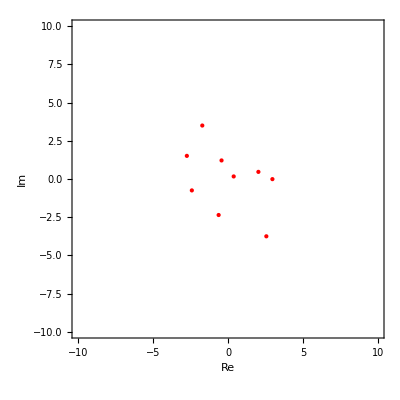

```mathematica
a=CoefficientList[Series[Exp[z  ϵ+I ϵ^2 +I ϵ^4 +I ϵ^5 +I  ϵ^7  +I  ϵ^8 - (1+ⅈ) ϵ^10],{ϵ,0,10}],ϵ];
aa=Part[a,{1,2,3,4,5,6,7,8,9,10}];
aa[[0]]=0;
q =Wronskian[({aa[[2]],aa[[5]],aa[[8]]}),z]//FullSimplify;
s = Solve[q == 0,z];

rt = Flatten[Values[s]]
ComplexListPlot[rt,PlotRange->{{-10,10},{-10,10}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Red,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}]
```

{Root-0.248Root[-675-44100 #1^3+315 #1^5+7 #1^10&,1]-0.2483240812881968,Root3.45Root[-675-44100 #1^3+315 #1^5+7 #1^10&,2]3.4457982056148104,Root-3.13-1.47 ⅈRoot[-675-44100 #1^3+315 #1^5+7 #1^10&,3]-3.1344885837348326,Root-3.13+1.47 ⅈRoot[-675-44100 #1^3+315 #1^5+7 #1^10&,4]-3.1344885837348326,Root-0.803-3.44 ⅈRoot[-675-44100 #1^3+315 #1^5+7 #1^10&,5]-0.8031810400670114,Root-0.803+3.44 ⅈRoot[-675-44100 #1^3+315 #1^5+7 #1^10&,6]-0.8031810400670114,Root0.124-0.215 ⅈRoot[-675-44100 #1^3+315 #1^5+7 #1^10&,7]0.12410737592104629,Root0.124+0.215 ⅈRoot[-675-44100 #1^3+315 #1^5+7 #1^10&,8]0.12410737592104629,Root2.21-2.71 ⅈRoot[-675-44100 #1^3+315 #1^5+7 #1^10&,9]2.214825185717491,Root2.21+2.71 ⅈRoot[-675-44100 #1^3+315 #1^5+7 #1^10&,10]2.214825185717491}

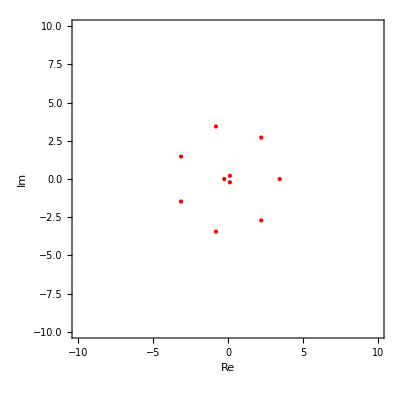

```mathematica
a=CoefficientList[Series[Exp[z  ϵ-2/3 ϵ^2 +1/5 ϵ^4 + 1/7 ϵ^5 + 4 ϵ^7 + 5 ϵ^ 8 + 6 ϵ^10+ 7 ϵ^11 + 8 ϵ^13],{ϵ,0,10}],ϵ];
aa=Part[a,{1,2,3,4,5,6,7,8,9,10}];
aa[[0]]=0;
q =Wronskian[({aa[[2]],aa[[4]],aa[[6]],aa[[8]]}),z]//FullSimplify;s = Solve[q == 0,z];
rt = Flatten[Values[s]]
ComplexListPlot[rt,PlotRange->{{-10,10},{-10,10}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Red,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}]
```

{Root-0.0276Root[-25-1190700 #1^3-315 #1^5+189 #1^10&,1]-0.027587511203151074,Root3.49Root[-25-1190700 #1^3-315 #1^5+189 #1^10&,2]3.491103188817686,Root-3.14-1.52 ⅈRoot[-25-1190700 #1^3-315 #1^5+189 #1^10&,3]-3.1442865697577793,Root-3.14+1.52 ⅈRoot[-25-1190700 #1^3-315 #1^5+189 #1^10&,4]-3.1442865697577793,Root-0.775-3.40 ⅈRoot[-25-1190700 #1^3-315 #1^5+189 #1^10&,5]-0.7754846613009445,Root-0.775+3.40 ⅈRoot[-25-1190700 #1^3-315 #1^5+189 #1^10&,6]-0.7754846613009445,Root0.0138-0.0239 ⅈRoot[-25-1190700 #1^3-315 #1^5+189 #1^10&,7]0.01379375837883119,Root0.0138+0.0239 ⅈRoot[-25-1190700 #1^3-315 #1^5+189 #1^10&,8]0.01379375837883119,Root2.17-2.73 ⅈRoot[-25-1190700 #1^3-315 #1^5+189 #1^10&,9]2.174219633872625,Root2.17+2.73 ⅈRoot[-25-1190700 #1^3-315 #1^5+189 #1^10&,10]2.174219633872625}

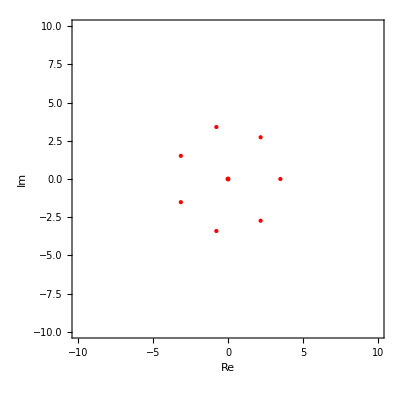

```mathematica
a=CoefficientList[Series[Exp[z  ϵ -1/45 ϵ^4 -1/189 ϵ^5 + 4 ϵ^7 + 5 ϵ^ 8 + 6 ϵ^10+ 7 ϵ^11 + 8 ϵ^13],{ϵ,0,10}],ϵ];
aa=Part[a,{1,2,3,4,5,6,7,8,9,10}];
aa[[0]]=0;
q =Wronskian[({aa[[2]],aa[[4]],aa[[6]],aa[[8]]}),z]//FullSimplify;s = Solve[q == 0,z];
rt = Flatten[Values[s]]
ComplexListPlot[rt,PlotRange->{{-10,10},{-10,10}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Red,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}]
```

{Root-0.179Root[{-5+#1^2&,-1269-567 #1-441000 #2^3-945 #2^5-441 #1 #2^5+70 #2^10&},{2,1}]-0.17916991276996191,Root3.52Root[{-5+#1^2&,-1269-567 #1-441000 #2^3-945 #2^5-441 #1 #2^5+70 #2^10&},{2,2}]3.5159396458285572,Root-3.15-1.54 ⅈRoot[{-5+#1^2&,-1269-567 #1-441000 #2^3-945 #2^5-441 #1 #2^5+70 #2^10&},{2,3}]-3.149931233112936,Root-3.15+1.54 ⅈRoot[{-5+#1^2&,-1269-567 #1-441000 #2^3-945 #2^5-441 #1 #2^5+70 #2^10&},{2,4}]-3.149931233112936,Root-0.760-3.38 ⅈRoot[{-5+#1^2&,-1269-567 #1-441000 #2^3-945 #2^5-441 #1 #2^5+70 #2^10&},{2,5}]-0.7597959778487653,Root-0.760+3.38 ⅈRoot[{-5+#1^2&,-1269-567 #1-441000 #2^3-945 #2^5-441 #1 #2^5+70 #2^10&},{2,6}]-0.7597959778487653,Root0.0896-0.155 ⅈRoot[{-5+#1^2&,-1269-567 #1-441000 #2^3-945 #2^5-441 #1 #2^5+70 #2^10&},{2,7}]0.0895975512586434,Root0.0896+0.155 ⅈRoot[{-5+#1^2&,-1269-567 #1-441000 #2^3-945 #2^5-441 #1 #2^5+70 #2^10&},{2,8}]0.0895975512586434,Root2.15-2.74 ⅈRoot[{-5+#1^2&,-1269-567 #1-441000 #2^3-945 #2^5-441 #1 #2^5+70 #2^10&},{2,9}]2.15174479317376,Root2.15+2.74 ⅈRoot[{-5+#1^2&,-1269-567 #1-441000 #2^3-945 #2^5-441 #1 #2^5+70 #2^10&},{2,10}]2.15174479317376}

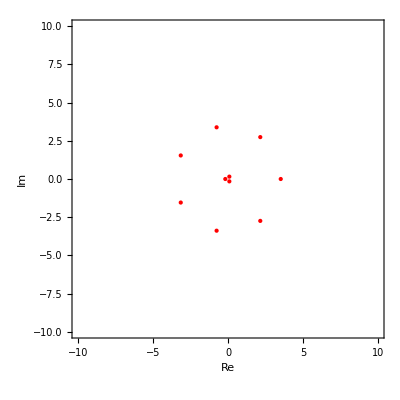

```mathematica
a=CoefficientList[Series[Exp[z  ϵ+(3Sqrt[5]-5)/30 ϵ^2 -(7Sqrt[5]+15)/350 ϵ^5 + 4 ϵ^7 + 5 ϵ^ 8 + 6 ϵ^10+ 7 ϵ^11 + 8 ϵ^13],{ϵ,0,10}],ϵ];
aa=Part[a,{1,2,3,4,5,6,7,8,9,10}];
aa[[0]]=0;
q =Wronskian[({aa[[2]],aa[[4]],aa[[6]],aa[[8]]}),z]//FullSimplify;s = Solve[q == 0,z];
rt = Flatten[Values[s]]
ComplexListPlot[rt,PlotRange->{{-10,10},{-10,10}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Red,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}]
```

{1,1,1,Root-3.32Root[639+517 #1+264 #1^2+105 #1^3+40 #1^4+6 #1^5+3 #1^6+#1^7&,1]-3.3205245675536696,Root-1.61-1.09 ⅈRoot[639+517 #1+264 #1^2+105 #1^3+40 #1^4+6 #1^5+3 #1^6+#1^7&,2]-1.6127852928988295,Root-1.61+1.09 ⅈRoot[639+517 #1+264 #1^2+105 #1^3+40 #1^4+6 #1^5+3 #1^6+#1^7&,3]-1.6127852928988295,Root-0.0510-2.25 ⅈRoot[639+517 #1+264 #1^2+105 #1^3+40 #1^4+6 #1^5+3 #1^6+#1^7&,4]-0.050974128857118745,Root-0.0510+2.25 ⅈRoot[639+517 #1+264 #1^2+105 #1^3+40 #1^4+6 #1^5+3 #1^6+#1^7&,5]-0.050974128857118745,Root1.82-2.59 ⅈRoot[639+517 #1+264 #1^2+105 #1^3+40 #1^4+6 #1^5+3 #1^6+#1^7&,6]1.824021705532783,Root1.82+2.59 ⅈRoot[639+517 #1+264 #1^2+105 #1^3+40 #1^4+6 #1^5+3 #1^6+#1^7&,7]1.824021705532783}

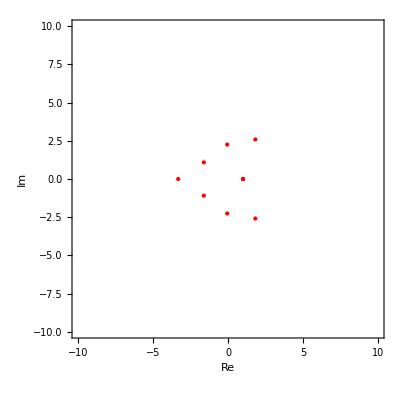

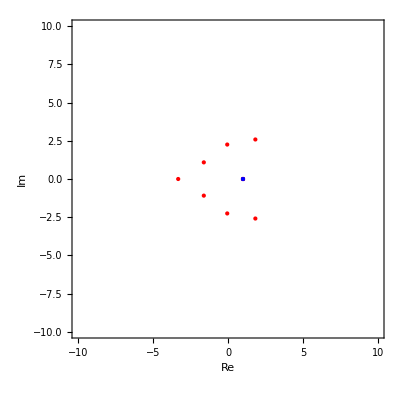

```mathematica
a=CoefficientList[Series[Exp[z  ϵ-2/3 ϵ^3 +1/5 ϵ^5 + 1/7 ϵ^7 + 5 ϵ^ 9 ],{ϵ,0,10}],ϵ];
aa=Part[a,{1,2,3,4,5,6,7,8,9,10}];
aa[[0]]=0;
q =Wronskian[({aa[[2]],aa[[4]],aa[[6]],aa[[8]]}),z]//FullSimplify;s = Solve[q == 0,z];
rt = Flatten[Values[s]]
A =ComplexListPlot[rt,PlotRange->{{-10,10},{-10,10}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Red,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}]
B=ComplexListPlot[{1},PlotRange->{{-10,10},{-10,10}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Blue,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}];
Show[A,B]
```

{1,1,1,Root-1.09Root[7+21 #1+42 #1^2+45 #1^3+30 #1^4+18 #1^5+9 #1^6+3 #1^7&,1]-1.089698138783443,Root-1.13-0.995 ⅈRoot[7+21 #1+42 #1^2+45 #1^3+30 #1^4+18 #1^5+9 #1^6+3 #1^7&,2]-1.1263605298271266,Root-1.13+0.995 ⅈRoot[7+21 #1+42 #1^2+45 #1^3+30 #1^4+18 #1^5+9 #1^6+3 #1^7&,3]-1.1263605298271266,Root-0.269-0.550 ⅈRoot[7+21 #1+42 #1^2+45 #1^3+30 #1^4+18 #1^5+9 #1^6+3 #1^7&,4]-0.26862799904051776,Root-0.269+0.550 ⅈRoot[7+21 #1+42 #1^2+45 #1^3+30 #1^4+18 #1^5+9 #1^6+3 #1^7&,5]-0.26862799904051776,Root0.440-1.53 ⅈRoot[7+21 #1+42 #1^2+45 #1^3+30 #1^4+18 #1^5+9 #1^6+3 #1^7&,6]0.43983759825936597,Root0.440+1.53 ⅈRoot[7+21 #1+42 #1^2+45 #1^3+30 #1^4+18 #1^5+9 #1^6+3 #1^7&,7]0.43983759825936597}

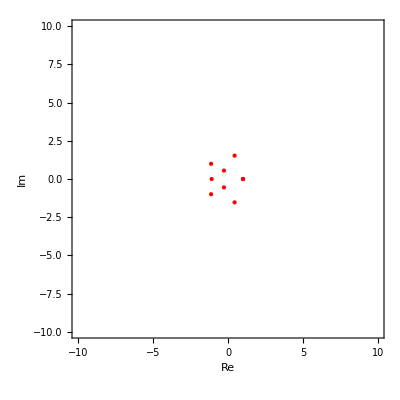

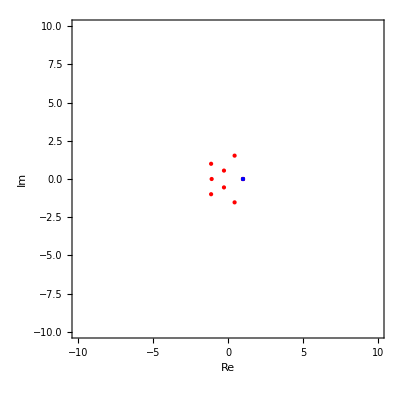

```mathematica
a=CoefficientList[Series[Exp[z  ϵ -1/45 ϵ^5 - 1/189 ϵ^7 + 5 ϵ^ 9 ],{ϵ,0,10}],ϵ];
aa=Part[a,{1,2,3,4,5,6,7,8,9,10}];
aa[[0]]=0;
q =Wronskian[({aa[[2]],aa[[4]],aa[[6]],aa[[8]]}),z]//FullSimplify;s = Solve[q == 0,z];
rt = Flatten[Values[s]]
A = ComplexListPlot[rt,PlotRange->{{-10,10},{-10,10}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Red,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}]
B=ComplexListPlot[{1},PlotRange->{{-10,10},{-10,10}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Blue,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}];
Show[A,B]
```

{1,1,1,Root-0.933Root[{-5+#1^2&,-162+72 #1-206 #2+90 #1 #2-132 #2^2+54 #1 #2^2-75 #2^3+27 #1 #2^3-35 #2^4+9 #1 #2^4-12 #2^5-6 #2^6-2 #2^7&},{2,1}]-0.9325786430408609,Root-0.788-1.22 ⅈRoot[{-5+#1^2&,-162+72 #1-206 #2+90 #1 #2-132 #2^2+54 #1 #2^2-75 #2^3+27 #1 #2^3-35 #2^4+9 #1 #2^4-12 #2^5-6 #2^6-2 #2^7&},{2,2}]-0.7875963188027576,Root-0.788+1.22 ⅈRoot[{-5+#1^2&,-162+72 #1-206 #2+90 #1 #2-132 #2^2+54 #1 #2^2-75 #2^3+27 #1 #2^3-35 #2^4+9 #1 #2^4-12 #2^5-6 #2^6-2 #2^7&},{2,3}]-0.7875963188027576,Root-0.358-0.318 ⅈRoot[{-5+#1^2&,-162+72 #1-206 #2+90 #1 #2-132 #2^2+54 #1 #2^2-75 #2^3+27 #1 #2^3-35 #2^4+9 #1 #2^4-12 #2^5-6 #2^6-2 #2^7&},{2,4}]-0.35774197480605935,Root-0.358+0.318 ⅈRoot[{-5+#1^2&,-162+72 #1-206 #2+90 #1 #2-132 #2^2+54 #1 #2^2-75 #2^3+27 #1 #2^3-35 #2^4+9 #1 #2^4-12 #2^5-6 #2^6-2 #2^7&},{2,5}]-0.35774197480605935,Root0.112-1.05 ⅈRoot[{-5+#1^2&,-162+72 #1-206 #2+90 #1 #2-132 #2^2+54 #1 #2^2-75 #2^3+27 #1 #2^3-35 #2^4+9 #1 #2^4-12 #2^5-6 #2^6-2 #2^7&},{2,6}]0.11162761512924742,Root0.112+1.05 ⅈRoot[{-5+#1^2&,-162+72 #1-206 #2+90 #1 #2-132 #2^2+54 #1 #2^2-75 #2^3+27 #1 #2^3-35 #2^4+9 #1 #2^4-12 #2^5-6 #2^6-2 #2^7&},{2,7}]0.11162761512924742}

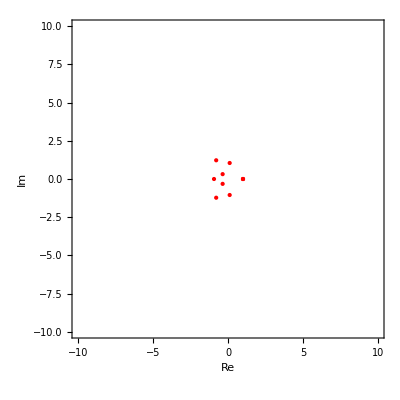

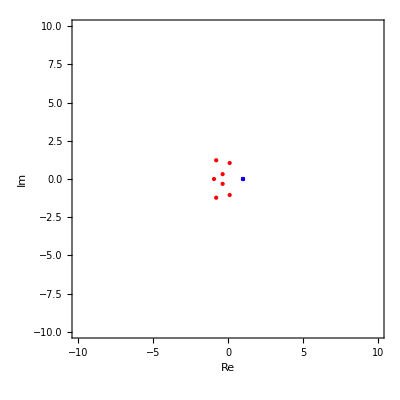

```mathematica
a=CoefficientList[Series[Exp[z  ϵ+(3Sqrt[5]-5)/30 ϵ^3  +(-7Sqrt[5]+15)/350 ϵ^ 7 ],{ϵ,0,10}],ϵ];
aa=Part[a,{1,2,3,4,5,6,7,8,9,10}];
aa[[0]]=0;
q =Wronskian[({aa[[2]],aa[[4]],aa[[6]],aa[[8]]}),z]//FullSimplify;s = Solve[q == 0,z];
rt = Flatten[Values[s]]
A=ComplexListPlot[rt,PlotRange->{{-10,10},{-10,10}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Red,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}]
B=ComplexListPlot[{1},PlotRange->{{-10,10},{-10,10}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Blue,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}];
Show[A,B]
```

{{z→0},{z→Root4.18Root[-4725-4725 #1-1575 #1^2-315 #1^4-45 #1^6+#1^9&,1]4.176392664255164},{z→Root-2.40-2.68 ⅈRoot[-4725-4725 #1-1575 #1^2-315 #1^4-45 #1^6+#1^9&,2]-2.3981762896088363},{z→Root-2.40+2.68 ⅈRoot[-4725-4725 #1-1575 #1^2-315 #1^4-45 #1^6+#1^9&,3]-2.3981762896088363},{z→Root-1.13-0.661 ⅈRoot[-4725-4725 #1-1575 #1^2-315 #1^4-45 #1^6+#1^9&,4]-1.1299616221340687},{z→Root-1.13+0.661 ⅈRoot[-4725-4725 #1-1575 #1^2-315 #1^4-45 #1^6+#1^9&,5]-1.1299616221340687},{z→Root-0.295-2.77 ⅈRoot[-4725-4725 #1-1575 #1^2-315 #1^4-45 #1^6+#1^9&,6]-0.29487210192987895},{z→Root-0.295+2.77 ⅈRoot[-4725-4725 #1-1575 #1^2-315 #1^4-45 #1^6+#1^9&,7]-0.29487210192987895},{z→Root1.73-1.89 ⅈRoot[-4725-4725 #1-1575 #1^2-315 #1^4-45 #1^6+#1^9&,8]1.734813681545202},{z→Root1.73+1.89 ⅈRoot[-4725-4725 #1-1575 #1^2-315 #1^4-45 #1^6+#1^9&,9]1.734813681545202}}

{0,Root4.18Root[-4725-4725 #1-1575 #1^2-315 #1^4-45 #1^6+#1^9&,1]4.176392664255164,Root-2.40-2.68 ⅈRoot[-4725-4725 #1-1575 #1^2-315 #1^4-45 #1^6+#1^9&,2]-2.3981762896088363,Root-2.40+2.68 ⅈRoot[-4725-4725 #1-1575 #1^2-315 #1^4-45 #1^6+#1^9&,3]-2.3981762896088363,Root-1.13-0.661 ⅈRoot[-4725-4725 #1-1575 #1^2-315 #1^4-45 #1^6+#1^9&,4]-1.1299616221340687,Root-1.13+0.661 ⅈRoot[-4725-4725 #1-1575 #1^2-315 #1^4-45 #1^6+#1^9&,5]-1.1299616221340687,Root-0.295-2.77 ⅈRoot[-4725-4725 #1-1575 #1^2-315 #1^4-45 #1^6+#1^9&,6]-0.29487210192987895,Root-0.295+2.77 ⅈRoot[-4725-4725 #1-1575 #1^2-315 #1^4-45 #1^6+#1^9&,7]-0.29487210192987895,Root1.73-1.89 ⅈRoot[-4725-4725 #1-1575 #1^2-315 #1^4-45 #1^6+#1^9&,8]1.734813681545202,Root1.73+1.89 ⅈRoot[-4725-4725 #1-1575 #1^2-315 #1^4-45 #1^6+#1^9&,9]1.734813681545202}

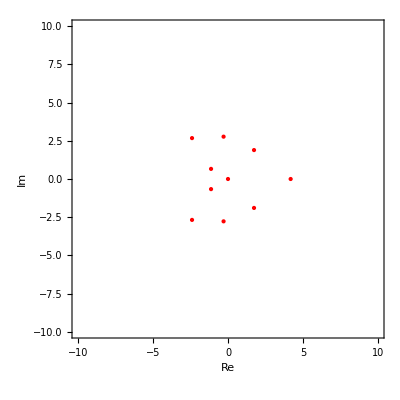

```mathematica
a=CoefficientList[Series[Exp[z  ϵ+ϵ^3  -ϵ^5+ ϵ^ 7 ],{ϵ,0,10}],ϵ];
aa=Part[a,{1,2,3,4,5,6,7,8,9,10}];
aa[[0]]=0;
q =Wronskian[({aa[[2]],aa[[4]],aa[[6]],aa[[8]]}),z]//FullSimplify;s = Solve[q == 0,z]
rt = Flatten[Values[s]]
A = ComplexListPlot[rt,PlotRange->{{-10,10},{-10,10}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Red,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}]
```

{{z→-2.33349-0.998752 ⅈ},{z→-2.33349+0.998752 ⅈ},{z→-1.01698},{z→-0.492736-1.62109 ⅈ},{z→-0.492736+1.62109 ⅈ},{z→1.18808-2.65768 ⅈ},{z→1.18808+2.65768 ⅈ},{z→1.22},{z→1.53664-0.18276 ⅈ},{z→1.53664+0.18276 ⅈ}}

{-2.33349-0.998752 ⅈ,-2.33349+0.998752 ⅈ,-1.01698,-0.492736-1.62109 ⅈ,-0.492736+1.62109 ⅈ,1.18808-2.65768 ⅈ,1.18808+2.65768 ⅈ,1.22,1.53664-0.18276 ⅈ,1.53664+0.18276 ⅈ}

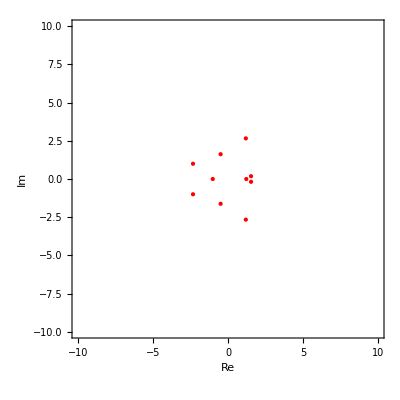

```mathematica
a=CoefficientList[Series[Exp[z  ϵ-0.32ϵ^3  -0.28 ϵ^5+0.063 ϵ^ 7 ],{ϵ,0,10}],ϵ];
aa=Part[a,{1,2,3,4,5,6,7,8,9,10}];
aa[[0]]=0;
q =Wronskian[({aa[[2]],aa[[4]],aa[[6]],aa[[8]]}),z]//FullSimplify;s = Solve[q == 0,z]
rt = Flatten[Values[s]]
A = ComplexListPlot[rt,PlotRange->{{-10,10},{-10,10}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Red,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}]
```

{{z→-1.35858+0.986843 ⅈ},{z→-0.958611-0.552771 ⅈ},{z→-0.851534-0.403627 ⅈ},{z→-0.775906-0.570919 ⅈ},{z→-0.207446+0.758629 ⅈ},{z→0.481685-1.76025 ⅈ},{z→0.667383+1.54143 ⅈ},{z→0.948369-0.0791637 ⅈ},{z→0.958565+0.0854989 ⅈ},{z→1.09607-0.00566585 ⅈ}}

{-1.35858+0.986843 ⅈ,-0.958611-0.552771 ⅈ,-0.851534-0.403627 ⅈ,-0.775906-0.570919 ⅈ,-0.207446+0.758629 ⅈ,0.481685-1.76025 ⅈ,0.667383+1.54143 ⅈ,0.948369-0.0791637 ⅈ,0.958565+0.0854989 ⅈ,1.09607-0.00566585 ⅈ}

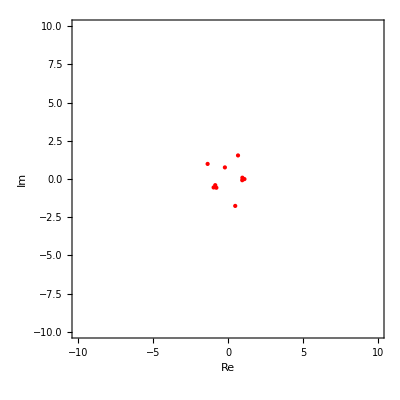

```mathematica
a=CoefficientList[Series[Exp[z  ϵ+(-0.029+0.028 I)ϵ^3 +(-0.032+0.0077 I) ϵ^5+(-0.0052-0.0016I)ϵ^ 7 ],{ϵ,0,10}],ϵ];
aa=Part[a,{1,2,3,4,5,6,7,8,9,10}];
aa[[0]]=0;
q =Wronskian[({aa[[2]],aa[[4]],aa[[6]],aa[[8]]}),z]//FullSimplify;s = Solve[q == 0,z]
rt = Flatten[Values[s]]
A = ComplexListPlot[rt,PlotRange->{{-10,10},{-10,10}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Red,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}]
```

{{z→-1.62252+0.603193 ⅈ},{z→-1.04264-0.253206 ⅈ},{z→-0.587998+0.813838 ⅈ},{z→-0.369933-0.876888 ⅈ},{z→-0.136685+0.0693853 ⅈ},{z→0.259672+0.853954 ⅈ},{z→0.270103-1.77246 ⅈ},{z→0.777324-0.854666 ⅈ},{z→1.16494+0.202532 ⅈ},{z→1.28774+1.21432 ⅈ}}

{-1.62252+0.603193 ⅈ,-1.04264-0.253206 ⅈ,-0.587998+0.813838 ⅈ,-0.369933-0.876888 ⅈ,-0.136685+0.0693853 ⅈ,0.259672+0.853954 ⅈ,0.270103-1.77246 ⅈ,0.777324-0.854666 ⅈ,1.16494+0.202532 ⅈ,1.28774+1.21432 ⅈ}

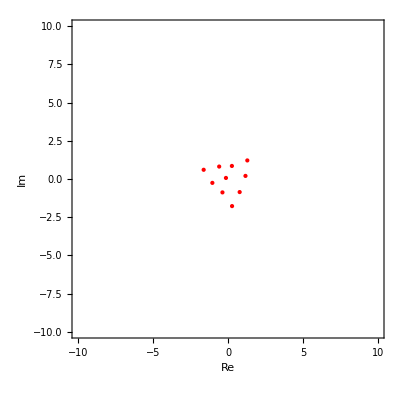

```mathematica
a=CoefficientList[Series[Exp[z  ϵ+(-0.06+0.098 I)ϵ^3 +(-0.0011+0.0045 I) ϵ^5+(0.0016+0.0013I)ϵ^ 7 ],{ϵ,0,10}],ϵ];
aa=Part[a,{1,2,3,4,5,6,7,8,9,10}];
aa[[0]]=0;
q =Wronskian[({aa[[2]],aa[[4]],aa[[6]],aa[[8]]}),z]//FullSimplify;s = Solve[q == 0,z]
rt = Flatten[Values[s]]
A = ComplexListPlot[rt,PlotRange->{{-10,10},{-10,10}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Red,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}]
```

```mathematica
CoefficientList[Series[Exp[z ϵ+∑_(j=1)^7 Subscript[κ, j] ϵ^(2j+1)],{ϵ,0,7}],ϵ]//Simplify
```

{1,z,z^2/2,z^3/6+κ_1,z^4/24+z κ_1,z^5/120+(z^2 κ_1)/2+κ_2,z^6/720+(z^3 κ_1)/6+κ_1^2/2+z κ_2,z^7/5040+(z^4 κ_1)/24+(z κ_1^2)/2+(z^2 κ_2)/2+κ_3}

```mathematica
5!!
```

15

```mathematica
a=CoefficientList[Series[Exp[z  ϵ +ⅈ ϵ^2    +ⅈ ϵ^8 +ⅈ ϵ^10+ⅈ ϵ^11+ⅈ ϵ^13],{ϵ,0,10}],ϵ];
aa=Part[a,{1,2,3,4,5,6,7,8,9,10}];
aa[[0]]=0;
q =Wronskian[({aa[[2]],aa[[5]],aa[[8]],aa[[10]]}),z]//FullSimplify;
s = Solve[q == 0,z];

rt = Flatten[Values[s]]
ComplexListPlot[rt,PlotRange->{{-10,10},{-10,10}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Red,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}]
```

{0,0,0,Root-3.25+1.84 ⅈRoot[{1+#1^2&,141120-28224 #1 #2^2+1008 #2^4-1120 #1 #2^6-308 #2^8+28 #1 #2^10+#2^12&},{2,1}]-3.246943839062588,Root-2.40+0.372 ⅈRoot[{1+#1^2&,141120-28224 #1 #2^2+1008 #2^4-1120 #1 #2^6-308 #2^8+28 #1 #2^10+#2^12&},{2,2}]-2.400366023541613,Root-1.84+3.25 ⅈRoot[{1+#1^2&,141120-28224 #1 #2^2+1008 #2^4-1120 #1 #2^6-308 #2^8+28 #1 #2^10+#2^12&},{2,3}]-1.8391777398089844,Root-1.56+1.56 ⅈRoot[{1+#1^2&,141120-28224 #1 #2^2+1008 #2^4-1120 #1 #2^6-308 #2^8+28 #1 #2^10+#2^12&},{2,4}]-1.5572508852201965,Root-1.47-1.47 ⅈRoot[{1+#1^2&,141120-28224 #1 #2^2+1008 #2^4-1120 #1 #2^6-308 #2^8+28 #1 #2^10+#2^12&},{2,5}]-1.4680216861295543,Root-0.372+2.40 ⅈRoot[{1+#1^2&,141120-28224 #1 #2^2+1008 #2^4-1120 #1 #2^6-308 #2^8+28 #1 #2^10+#2^12&},{2,6}]-0.3721606770545355,Root0.372-2.40 ⅈRoot[{1+#1^2&,141120-28224 #1 #2^2+1008 #2^4-1120 #1 #2^6-308 #2^8+28 #1 #2^10+#2^12&},{2,7}]0.3721606770545355,Root1.47+1.47 ⅈRoot[{1+#1^2&,141120-28224 #1 #2^2+1008 #2^4-1120 #1 #2^6-308 #2^8+28 #1 #2^10+#2^12&},{2,8}]1.4680216861295543,Root1.56-1.56 ⅈRoot[{1+#1^2&,141120-28224 #1 #2^2+1008 #2^4-1120 #1 #2^6-308 #2^8+28 #1 #2^10+#2^12&},{2,9}]1.5572508852201965,Root1.84-3.25 ⅈRoot[{1+#1^2&,141120-28224 #1 #2^2+1008 #2^4-1120 #1 #2^6-308 #2^8+28 #1 #2^10+#2^12&},{2,10}]1.8391777398089844,Root2.40-0.372 ⅈRoot[{1+#1^2&,141120-28224 #1 #2^2+1008 #2^4-1120 #1 #2^6-308 #2^8+28 #1 #2^10+#2^12&},{2,11}]2.400366023541613,Root3.25-1.84 ⅈRoot[{1+#1^2&,141120-28224 #1 #2^2+1008 #2^4-1120 #1 #2^6-308 #2^8+28 #1 #2^10+#2^12&},{2,12}]3.246943839062588}

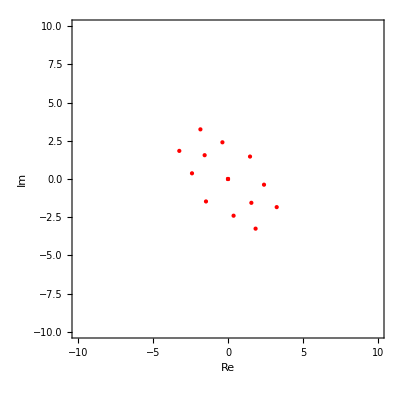

{Root-4.17+2.03 ⅈRoot[{1+#1^2&,72072000-4032000 #1+44352000 #2-22545600 #2^2+448000 #1 #2^2-31046400 #2^3-2433200 #2^4+112000 #1 #2^4-147840 #2^5-86240 #2^6-73920 #2^7-9460 #2^8+308 #2^10+11 #2^12&},{2,1}]-4.167147879244388,Root-4.15-2.07 ⅈRoot[{1+#1^2&,72072000-4032000 #1+44352000 #2-22545600 #2^2+448000 #1 #2^2-31046400 #2^3-2433200 #2^4+112000 #1 #2^4-147840 #2^5-86240 #2^6-73920 #2^7-9460 #2^8+308 #2^10+11 #2^12&},{2,2}]-4.151716515790381,Root-2.35+4.00 ⅈRoot[{1+#1^2&,72072000-4032000 #1+44352000 #2-22545600 #2^2+448000 #1 #2^2-31046400 #2^3-2433200 #2^4+112000 #1 #2^4-147840 #2^5-86240 #2^6-73920 #2^7-9460 #2^8+308 #2^10+11 #2^12&},{2,3}]-2.3489868042232644,Root-2.32-3.98 ⅈRoot[{1+#1^2&,72072000-4032000 #1+44352000 #2-22545600 #2^2+448000 #1 #2^2-31046400 #2^3-2433200 #2^4+112000 #1 #2^4-147840 #2^5-86240 #2^6-73920 #2^7-9460 #2^8+308 #2^10+11 #2^12&},{2,4}]-2.323055006340573,Root-1.17-0.697 ⅈRoot[{1+#1^2&,72072000-4032000 #1+44352000 #2-22545600 #2^2+448000 #1 #2^2-31046400 #2^3-2433200 #2^4+112000 #1 #2^4-147840 #2^5-86240 #2^6-73920 #2^7-9460 #2^8+308 #2^10+11 #2^12&},{2,5}]-1.171169434121498,Root-1.10+0.735 ⅈRoot[{1+#1^2&,72072000-4032000 #1+44352000 #2-22545600 #2^2+448000 #1 #2^2-31046400 #2^3-2433200 #2^4+112000 #1 #2^4-147840 #2^5-86240 #2^6-73920 #2^7-9460 #2^8+308 #2^10+11 #2^12&},{2,6}]-1.0988890191972824,Root0.951-7.19 ⅈRoot[{1+#1^2&,72072000-4032000 #1+44352000 #2-22545600 #2^2+448000 #1 #2^2-31046400 #2^3-2433200 #2^4+112000 #1 #2^4-147840 #2^5-86240 #2^6-73920 #2^7-9460 #2^8+308 #2^10+11 #2^12&},{2,7}]0.9510252777444883,Root0.953+7.19 ⅈRoot[{1+#1^2&,72072000-4032000 #1+44352000 #2-22545600 #2^2+448000 #1 #2^2-31046400 #2^3-2433200 #2^4+112000 #1 #2^4-147840 #2^5-86240 #2^6-73920 #2^7-9460 #2^8+308 #2^10+11 #2^12&},{2,8}]0.953472500784649,Root1.37-0.0123 ⅈRoot[{1+#1^2&,72072000-4032000 #1+44352000 #2-22545600 #2^2+448000 #1 #2^2-31046400 #2^3-2433200 #2^4+112000 #1 #2^4-147840 #2^5-86240 #2^6-73920 #2^7-9460 #2^8+308 #2^10+11 #2^12&},{2,9}]1.370492774251152,Root2.85-3.06 ⅈRoot[{1+#1^2&,72072000-4032000 #1+44352000 #2-22545600 #2^2+448000 #1 #2^2-31046400 #2^3-2433200 #2^4+112000 #1 #2^4-147840 #2^5-86240 #2^6-73920 #2^7-9460 #2^8+308 #2^10+11 #2^12&},{2,10}]2.8495222121845982,Root2.87+3.06 ⅈRoot[{1+#1^2&,72072000-4032000 #1+44352000 #2-22545600 #2^2+448000 #1 #2^2-31046400 #2^3-2433200 #2^4+112000 #1 #2^4-147840 #2^5-86240 #2^6-73920 #2^7-9460 #2^8+308 #2^10+11 #2^12&},{2,11}]2.8694108894877393,Root6.27-3.67 × 10^-3 ⅈRoot[{1+#1^2&,72072000-4032000 #1+44352000 #2-22545600 #2^2+448000 #1 #2^2-31046400 #2^3-2433200 #2^4+112000 #1 #2^4-147840 #2^5-86240 #2^6-73920 #2^7-9460 #2^8+308 #2^10+11 #2^12&},{2,12}]6.267041004464761}

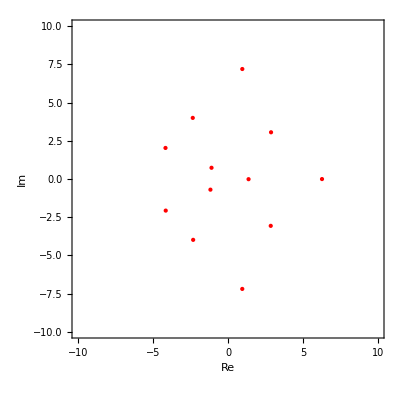

```mathematica
a=CoefficientList[Series[Exp[z  ϵ+ ϵ^2 + 4  ϵ^4 +7 ϵ^5 +  2  ϵ^7  +(5ⅈ)/11  ϵ^8 + (5ⅈ)/13  ϵ^10],{ϵ,0,10}],ϵ];
aa=Part[a,{1,2,3,4,5,6,7,8,9,10}];
aa[[0]]=0;
q =Wronskian[({aa[[2]],aa[[5]],aa[[8]]}),z]//FullSimplify;
s = Solve[q == 0,z];

rt = Flatten[Values[s]]
ComplexListPlot[rt,PlotRange->{{-10,10},{-10,10}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Red,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}]
```

{Root-3.29+0.796 ⅈRoot[{1+#1^2&,31207556800-21463142400 #1-558835200 #2-37362124800 #1 #2+290565273600 #2^2-17242948800 #1 #2^2+181062604800 #2^3+2514758400 #1 #2^3+12935538000 #2^4+59880643200 #1 #2^4+2263282560 #2^5+11639738880 #1 #2^5+646652160 #2^6-8981280 #1 #2^6-4364902080 #1 #2^7-18764460 #2^8-727483680 #1 #2^8+18187092 #1 #2^10+5845851 #2^12&},{2,1}]-3.2947181250127833,Root-2.46-2.30 ⅈRoot[{1+#1^2&,31207556800-21463142400 #1-558835200 #2-37362124800 #1 #2+290565273600 #2^2-17242948800 #1 #2^2+181062604800 #2^3+2514758400 #1 #2^3+12935538000 #2^4+59880643200 #1 #2^4+2263282560 #2^5+11639738880 #1 #2^5+646652160 #2^6-8981280 #1 #2^6-4364902080 #1 #2^7-18764460 #2^8-727483680 #1 #2^8+18187092 #1 #2^10+5845851 #2^12&},{2,2}]-2.4553824576528074,Root-1.80+1.91 ⅈRoot[{1+#1^2&,31207556800-21463142400 #1-558835200 #2-37362124800 #1 #2+290565273600 #2^2-17242948800 #1 #2^2+181062604800 #2^3+2514758400 #1 #2^3+12935538000 #2^4+59880643200 #1 #2^4+2263282560 #2^5+11639738880 #1 #2^5+646652160 #2^6-8981280 #1 #2^6-4364902080 #1 #2^7-18764460 #2^8-727483680 #1 #2^8+18187092 #1 #2^10+5845851 #2^12&},{2,3}]-1.7965997032272714,Root-1.40-0.467 ⅈRoot[{1+#1^2&,31207556800-21463142400 #1-558835200 #2-37362124800 #1 #2+290565273600 #2^2-17242948800 #1 #2^2+181062604800 #2^3+2514758400 #1 #2^3+12935538000 #2^4+59880643200 #1 #2^4+2263282560 #2^5+11639738880 #1 #2^5+646652160 #2^6-8981280 #1 #2^6-4364902080 #1 #2^7-18764460 #2^8-727483680 #1 #2^8+18187092 #1 #2^10+5845851 #2^12&},{2,4}]-1.4001627496565696,Root-0.667-2.62 ⅈRoot[{1+#1^2&,31207556800-21463142400 #1-558835200 #2-37362124800 #1 #2+290565273600 #2^2-17242948800 #1 #2^2+181062604800 #2^3+2514758400 #1 #2^3+12935538000 #2^4+59880643200 #1 #2^4+2263282560 #2^5+11639738880 #1 #2^5+646652160 #2^6-8981280 #1 #2^6-4364902080 #1 #2^7-18764460 #2^8-727483680 #1 #2^8+18187092 #1 #2^10+5845851 #2^12&},{2,5}]-0.6667597538230556,Root-0.481+3.91 ⅈRoot[{1+#1^2&,31207556800-21463142400 #1-558835200 #2-37362124800 #1 #2+290565273600 #2^2-17242948800 #1 #2^2+181062604800 #2^3+2514758400 #1 #2^3+12935538000 #2^4+59880643200 #1 #2^4+2263282560 #2^5+11639738880 #1 #2^5+646652160 #2^6-8981280 #1 #2^6-4364902080 #1 #2^7-18764460 #2^8-727483680 #1 #2^8+18187092 #1 #2^10+5845851 #2^12&},{2,6}]-0.4812225581228951,Root-0.0732-0.301 ⅈRoot[{1+#1^2&,31207556800-21463142400 #1-558835200 #2-37362124800 #1 #2+290565273600 #2^2-17242948800 #1 #2^2+181062604800 #2^3+2514758400 #1 #2^3+12935538000 #2^4+59880643200 #1 #2^4+2263282560 #2^5+11639738880 #1 #2^5+646652160 #2^6-8981280 #1 #2^6-4364902080 #1 #2^7-18764460 #2^8-727483680 #1 #2^8+18187092 #1 #2^10+5845851 #2^12&},{2,7}]-0.0731636642482985,Root0.138+0.390 ⅈRoot[{1+#1^2&,31207556800-21463142400 #1-558835200 #2-37362124800 #1 #2+290565273600 #2^2-17242948800 #1 #2^2+181062604800 #2^3+2514758400 #1 #2^3+12935538000 #2^4+59880643200 #1 #2^4+2263282560 #2^5+11639738880 #1 #2^5+646652160 #2^6-8981280 #1 #2^6-4364902080 #1 #2^7-18764460 #2^8-727483680 #1 #2^8+18187092 #1 #2^10+5845851 #2^12&},{2,8}]0.1379706669636597,Root1.08+1.75 ⅈRoot[{1+#1^2&,31207556800-21463142400 #1-558835200 #2-37362124800 #1 #2+290565273600 #2^2-17242948800 #1 #2^2+181062604800 #2^3+2514758400 #1 #2^3+12935538000 #2^4+59880643200 #1 #2^4+2263282560 #2^5+11639738880 #1 #2^5+646652160 #2^6-8981280 #1 #2^6-4364902080 #1 #2^7-18764460 #2^8-727483680 #1 #2^8+18187092 #1 #2^10+5845851 #2^12&},{2,9}]1.082851395144269,Root2.30-3.74 ⅈRoot[{1+#1^2&,31207556800-21463142400 #1-558835200 #2-37362124800 #1 #2+290565273600 #2^2-17242948800 #1 #2^2+181062604800 #2^3+2514758400 #1 #2^3+12935538000 #2^4+59880643200 #1 #2^4+2263282560 #2^5+11639738880 #1 #2^5+646652160 #2^6-8981280 #1 #2^6-4364902080 #1 #2^7-18764460 #2^8-727483680 #1 #2^8+18187092 #1 #2^10+5845851 #2^12&},{2,10}]2.297135648706509,Root2.79-0.764 ⅈRoot[{1+#1^2&,31207556800-21463142400 #1-558835200 #2-37362124800 #1 #2+290565273600 #2^2-17242948800 #1 #2^2+181062604800 #2^3+2514758400 #1 #2^3+12935538000 #2^4+59880643200 #1 #2^4+2263282560 #2^5+11639738880 #1 #2^5+646652160 #2^6-8981280 #1 #2^6-4364902080 #1 #2^7-18764460 #2^8-727483680 #1 #2^8+18187092 #1 #2^10+5845851 #2^12&},{2,11}]2.785449239584705,Root3.86+1.43 ⅈRoot[{1+#1^2&,31207556800-21463142400 #1-558835200 #2-37362124800 #1 #2+290565273600 #2^2-17242948800 #1 #2^2+181062604800 #2^3+2514758400 #1 #2^3+12935538000 #2^4+59880643200 #1 #2^4+2263282560 #2^5+11639738880 #1 #2^5+646652160 #2^6-8981280 #1 #2^6-4364902080 #1 #2^7-18764460 #2^8-727483680 #1 #2^8+18187092 #1 #2^10+5845851 #2^12&},{2,12}]3.864602061344538}

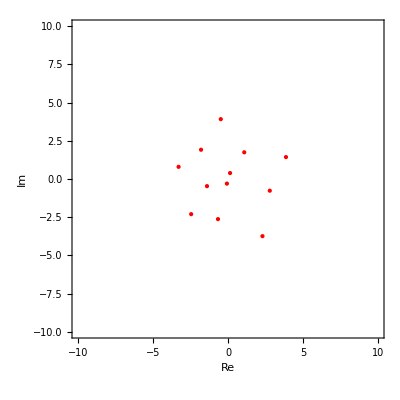

```mathematica
a=CoefficientList[Series[Exp[z  ϵ+ ⅈ/9 ϵ^2 + (4ⅈ)/9   ϵ^4 +(7ⅈ)/9  ϵ^5 +  (2ⅈ)/9 ϵ^7  +(5ⅈ)/11  ϵ^8 + (5ⅈ)/13  ϵ^10],{ϵ,0,10}],ϵ];
aa=Part[a,{1,2,3,4,5,6,7,8,9,10}];
aa[[0]]=0;
q =Wronskian[({aa[[2]],aa[[5]],aa[[8]]}),z]//FullSimplify;
s = Solve[q == 0,z];

rt = Flatten[Values[s]]
ComplexListPlot[rt,PlotRange->{{-10,10},{-10,10}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Red,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}]
```

{Root-4.84+2.99 ⅈRoot[{1+#1^2&,-206418625+194128298 #1-35013440 #2-16903040 #1 #2+37339176 #2^2+48860350 #1 #2^2+2414720 #2^3+8451520 #1 #2^3+4999225 #2^4+2753100 #1 #2^4+340032 #2^5+150920 #2^6-528220 #1 #2^6-14784 #1 #2^7-35035 #2^8-5390 #1 #2^8+1078 #1 #2^10+11 #2^12&},{2,1}]-4.8441746061399,Root-4.54+5.76 ⅈRoot[{1+#1^2&,-206418625+194128298 #1-35013440 #2-16903040 #1 #2+37339176 #2^2+48860350 #1 #2^2+2414720 #2^3+8451520 #1 #2^3+4999225 #2^4+2753100 #1 #2^4+340032 #2^5+150920 #2^6-528220 #1 #2^6-14784 #1 #2^7-35035 #2^8-5390 #1 #2^8+1078 #1 #2^10+11 #2^12&},{2,2}]-4.539748278486875,Root-3.90-0.0432 ⅈRoot[{1+#1^2&,-206418625+194128298 #1-35013440 #2-16903040 #1 #2+37339176 #2^2+48860350 #1 #2^2+2414720 #2^3+8451520 #1 #2^3+4999225 #2^4+2753100 #1 #2^4+340032 #2^5+150920 #2^6-528220 #1 #2^6-14784 #1 #2^7-35035 #2^8-5390 #1 #2^8+1078 #1 #2^10+11 #2^12&},{2,3}]-3.9048486105466167,Root-2.05+3.95 ⅈRoot[{1+#1^2&,-206418625+194128298 #1-35013440 #2-16903040 #1 #2+37339176 #2^2+48860350 #1 #2^2+2414720 #2^3+8451520 #1 #2^3+4999225 #2^4+2753100 #1 #2^4+340032 #2^5+150920 #2^6-528220 #1 #2^6-14784 #1 #2^7-35035 #2^8-5390 #1 #2^8+1078 #1 #2^10+11 #2^12&},{2,4}]-2.0460975233824086,Root-1.56+1.59 ⅈRoot[{1+#1^2&,-206418625+194128298 #1-35013440 #2-16903040 #1 #2+37339176 #2^2+48860350 #1 #2^2+2414720 #2^3+8451520 #1 #2^3+4999225 #2^4+2753100 #1 #2^4+340032 #2^5+150920 #2^6-528220 #1 #2^6-14784 #1 #2^7-35035 #2^8-5390 #1 #2^8+1078 #1 #2^10+11 #2^12&},{2,5}]-1.5570514655995622,Root-1.14-2.81 ⅈRoot[{1+#1^2&,-206418625+194128298 #1-35013440 #2-16903040 #1 #2+37339176 #2^2+48860350 #1 #2^2+2414720 #2^3+8451520 #1 #2^3+4999225 #2^4+2753100 #1 #2^4+340032 #2^5+150920 #2^6-528220 #1 #2^6-14784 #1 #2^7-35035 #2^8-5390 #1 #2^8+1078 #1 #2^10+11 #2^12&},{2,6}]-1.135105488354727,Root0.440+2.71 ⅈRoot[{1+#1^2&,-206418625+194128298 #1-35013440 #2-16903040 #1 #2+37339176 #2^2+48860350 #1 #2^2+2414720 #2^3+8451520 #1 #2^3+4999225 #2^4+2753100 #1 #2^4+340032 #2^5+150920 #2^6-528220 #1 #2^6-14784 #1 #2^7-35035 #2^8-5390 #1 #2^8+1078 #1 #2^10+11 #2^12&},{2,7}]0.43985590933267327,Root1.62-4.45 ⅈRoot[{1+#1^2&,-206418625+194128298 #1-35013440 #2-16903040 #1 #2+37339176 #2^2+48860350 #1 #2^2+2414720 #2^3+8451520 #1 #2^3+4999225 #2^4+2753100 #1 #2^4+340032 #2^5+150920 #2^6-528220 #1 #2^6-14784 #1 #2^7-35035 #2^8-5390 #1 #2^8+1078 #1 #2^10+11 #2^12&},{2,8}]1.6239433188542605,Root1.73-1.25 ⅈRoot[{1+#1^2&,-206418625+194128298 #1-35013440 #2-16903040 #1 #2+37339176 #2^2+48860350 #1 #2^2+2414720 #2^3+8451520 #1 #2^3+4999225 #2^4+2753100 #1 #2^4+340032 #2^5+150920 #2^6-528220 #1 #2^6-14784 #1 #2^7-35035 #2^8-5390 #1 #2^8+1078 #1 #2^10+11 #2^12&},{2,9}]1.7256496219898356,Root4.31+0.208 ⅈRoot[{1+#1^2&,-206418625+194128298 #1-35013440 #2-16903040 #1 #2+37339176 #2^2+48860350 #1 #2^2+2414720 #2^3+8451520 #1 #2^3+4999225 #2^4+2753100 #1 #2^4+340032 #2^5+150920 #2^6-528220 #1 #2^6-14784 #1 #2^7-35035 #2^8-5390 #1 #2^8+1078 #1 #2^10+11 #2^12&},{2,10}]4.312172889540479,Root4.95-6.14 ⅈRoot[{1+#1^2&,-206418625+194128298 #1-35013440 #2-16903040 #1 #2+37339176 #2^2+48860350 #1 #2^2+2414720 #2^3+8451520 #1 #2^3+4999225 #2^4+2753100 #1 #2^4+340032 #2^5+150920 #2^6-528220 #1 #2^6-14784 #1 #2^7-35035 #2^8-5390 #1 #2^8+1078 #1 #2^10+11 #2^12&},{2,11}]4.9461304939841355,Root4.98-2.52 ⅈRoot[{1+#1^2&,-206418625+194128298 #1-35013440 #2-16903040 #1 #2+37339176 #2^2+48860350 #1 #2^2+2414720 #2^3+8451520 #1 #2^3+4999225 #2^4+2753100 #1 #2^4+340032 #2^5+150920 #2^6-528220 #1 #2^6-14784 #1 #2^7-35035 #2^8-5390 #1 #2^8+1078 #1 #2^10+11 #2^12&},{2,12}]4.979273738808705}

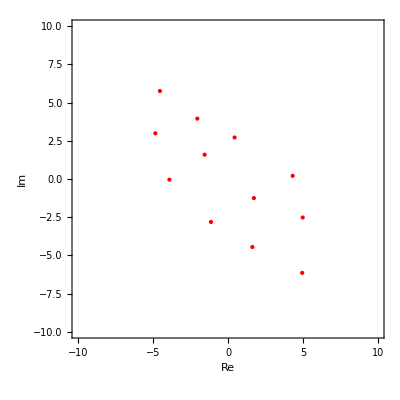

```mathematica
a=CoefficientList[Series[Exp[z  ϵ+ (7ⅈ)/2 ϵ^2 + (7ⅈ)/4   ϵ^4 +(7ⅈ)/5  ϵ^5 +   ϵ^7  +(5ⅈ)/11  ϵ^8 + (5ⅈ)/13  ϵ^10],{ϵ,0,10}],ϵ];
aa=Part[a,{1,2,3,4,5,6,7,8,9,10}];
aa[[0]]=0;
q =Wronskian[({aa[[2]],aa[[5]],aa[[8]]}),z]//FullSimplify;
s = Solve[q == 0,z];

rt = Flatten[Values[s]]
ComplexListPlot[rt,PlotRange->{{-10,10},{-10,10}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Red,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}]
```

{Root-2.97+1.07 ⅈRoot[{1+#1^2&,4312000-1344000 #1-985600 #2+1108800 #2^2+448000 #1 #2^2-1478400 #2^3-215600 #2^4+112000 #1 #2^4+49280 #2^5-12320 #2^6-10560 #2^7-220 #2^8+308 #2^10+11 #2^12&},{2,1}]-2.9713955048902183,Root-2.73-1.19 ⅈRoot[{1+#1^2&,4312000-1344000 #1-985600 #2+1108800 #2^2+448000 #1 #2^2-1478400 #2^3-215600 #2^4+112000 #1 #2^4+49280 #2^5-12320 #2^6-10560 #2^7-220 #2^8+308 #2^10+11 #2^12&},{2,2}]-2.731759490194755,Root-1.92+3.56 ⅈRoot[{1+#1^2&,4312000-1344000 #1-985600 #2+1108800 #2^2+448000 #1 #2^2-1478400 #2^3-215600 #2^4+112000 #1 #2^4+49280 #2^5-12320 #2^6-10560 #2^7-220 #2^8+308 #2^10+11 #2^12&},{2,3}]-1.9184872821498276,Root-1.85-3.43 ⅈRoot[{1+#1^2&,4312000-1344000 #1-985600 #2+1108800 #2^2+448000 #1 #2^2-1478400 #2^3-215600 #2^4+112000 #1 #2^4+49280 #2^5-12320 #2^6-10560 #2^7-220 #2^8+308 #2^10+11 #2^12&},{2,4}]-1.848976828311029,Root-0.489-1.21 ⅈRoot[{1+#1^2&,4312000-1344000 #1-985600 #2+1108800 #2^2+448000 #1 #2^2-1478400 #2^3-215600 #2^4+112000 #1 #2^4+49280 #2^5-12320 #2^6-10560 #2^7-220 #2^8+308 #2^10+11 #2^12&},{2,5}]-0.489152462831001,Root-0.174+1.39 ⅈRoot[{1+#1^2&,4312000-1344000 #1-985600 #2+1108800 #2^2+448000 #1 #2^2-1478400 #2^3-215600 #2^4+112000 #1 #2^4+49280 #2^5-12320 #2^6-10560 #2^7-220 #2^8+308 #2^10+11 #2^12&},{2,6}]-0.1740286977379152,Root0.561-5.56 ⅈRoot[{1+#1^2&,4312000-1344000 #1-985600 #2+1108800 #2^2+448000 #1 #2^2-1478400 #2^3-215600 #2^4+112000 #1 #2^4+49280 #2^5-12320 #2^6-10560 #2^7-220 #2^8+308 #2^10+11 #2^12&},{2,7}]0.5606470407683409,Root0.585+5.59 ⅈRoot[{1+#1^2&,4312000-1344000 #1-985600 #2+1108800 #2^2+448000 #1 #2^2-1478400 #2^3-215600 #2^4+112000 #1 #2^4+49280 #2^5-12320 #2^6-10560 #2^7-220 #2^8+308 #2^10+11 #2^12&},{2,8}]0.5845924795201436,Root1.43+4.37 × 10^-3 ⅈRoot[{1+#1^2&,4312000-1344000 #1-985600 #2+1108800 #2^2+448000 #1 #2^2-1478400 #2^3-215600 #2^4+112000 #1 #2^4+49280 #2^5-12320 #2^6-10560 #2^7-220 #2^8+308 #2^10+11 #2^12&},{2,9}]1.430242536484081,Root1.84-2.40 ⅈRoot[{1+#1^2&,4312000-1344000 #1-985600 #2+1108800 #2^2+448000 #1 #2^2-1478400 #2^3-215600 #2^4+112000 #1 #2^4+49280 #2^5-12320 #2^6-10560 #2^7-220 #2^8+308 #2^10+11 #2^12&},{2,10}]1.844779241942452,Root2.06+2.26 ⅈRoot[{1+#1^2&,4312000-1344000 #1-985600 #2+1108800 #2^2+448000 #1 #2^2-1478400 #2^3-215600 #2^4+112000 #1 #2^4+49280 #2^5-12320 #2^6-10560 #2^7-220 #2^8+308 #2^10+11 #2^12&},{2,11}]2.058270161506409,Root3.66-0.0910 ⅈRoot[{1+#1^2&,4312000-1344000 #1-985600 #2+1108800 #2^2+448000 #1 #2^2-1478400 #2^3-215600 #2^4+112000 #1 #2^4+49280 #2^5-12320 #2^6-10560 #2^7-220 #2^8+308 #2^10+11 #2^12&},{2,12}]3.6552688058933196}

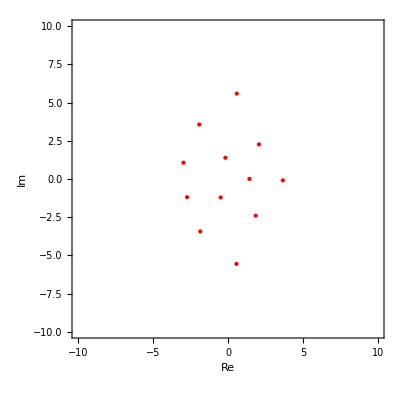

```mathematica
a=CoefficientList[Series[Exp[z  ϵ+  ϵ^2 + ϵ^4 + ϵ^5 +  ϵ^7  +(5ⅈ)/11  ϵ^8 + (5ⅈ)/13  ϵ^10],{ϵ,0,10}],ϵ];
aa=Part[a,{1,2,3,4,5,6,7,8,9,10}];
aa[[0]]=0;
q =Wronskian[({aa[[2]],aa[[5]],aa[[8]]}),z]//FullSimplify;
s = Solve[q == 0,z];

rt = Flatten[Values[s]]
ComplexListPlot[rt,PlotRange->{{-10,10},{-10,10}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Red,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}]
```

{Root-3.48+0.120 ⅈRoot[{1+#1^2&,-705600+201600 #1-985600 #2+1030400 #2^2-1355200 #1 #2^2+985600 #2^3+492800 #1 #2^3+154000 #2^4+235200 #1 #2^4+49280 #2^5+98560 #1 #2^5+24640 #2^6-12320 #1 #2^6-10560 #1 #2^7-2860 #2^8-3080 #1 #2^8+308 #1 #2^10+11 #2^12&},{2,1}]-3.479865184802695,Root-3.23+2.53 ⅈRoot[{1+#1^2&,-705600+201600 #1-985600 #2+1030400 #2^2-1355200 #1 #2^2+985600 #2^3+492800 #1 #2^3+154000 #2^4+235200 #1 #2^4+49280 #2^5+98560 #1 #2^5+24640 #2^6-12320 #1 #2^6-10560 #1 #2^7-2860 #2^8-3080 #1 #2^8+308 #1 #2^10+11 #2^12&},{2,2}]-3.2254275565335395,Root-2.07-1.88 ⅈRoot[{1+#1^2&,-705600+201600 #1-985600 #2+1030400 #2^2-1355200 #1 #2^2+985600 #2^3+492800 #1 #2^3+154000 #2^4+235200 #1 #2^4+49280 #2^5+98560 #1 #2^5+24640 #2^6-12320 #1 #2^6-10560 #1 #2^7-2860 #2^8-3080 #1 #2^8+308 #1 #2^10+11 #2^12&},{2,3}]-2.0697054093173644,Root-1.72+4.43 ⅈRoot[{1+#1^2&,-705600+201600 #1-985600 #2+1030400 #2^2-1355200 #1 #2^2+985600 #2^3+492800 #1 #2^3+154000 #2^4+235200 #1 #2^4+49280 #2^5+98560 #1 #2^5+24640 #2^6-12320 #1 #2^6-10560 #1 #2^7-2860 #2^8-3080 #1 #2^8+308 #1 #2^10+11 #2^12&},{2,4}]-1.7152044247595688,Root-0.995+1.56 ⅈRoot[{1+#1^2&,-705600+201600 #1-985600 #2+1030400 #2^2-1355200 #1 #2^2+985600 #2^3+492800 #1 #2^3+154000 #2^4+235200 #1 #2^4+49280 #2^5+98560 #1 #2^5+24640 #2^6-12320 #1 #2^6-10560 #1 #2^7-2860 #2^8-3080 #1 #2^8+308 #1 #2^10+11 #2^12&},{2,5}]-0.9953666934485433,Root-0.460-0.0824 ⅈRoot[{1+#1^2&,-705600+201600 #1-985600 #2+1030400 #2^2-1355200 #1 #2^2+985600 #2^3+492800 #1 #2^3+154000 #2^4+235200 #1 #2^4+49280 #2^5+98560 #1 #2^5+24640 #2^6-12320 #1 #2^6-10560 #1 #2^7-2860 #2^8-3080 #1 #2^8+308 #1 #2^10+11 #2^12&},{2,6}]-0.4601302322924559,Root-0.100-3.20 ⅈRoot[{1+#1^2&,-705600+201600 #1-985600 #2+1030400 #2^2-1355200 #1 #2^2+985600 #2^3+492800 #1 #2^3+154000 #2^4+235200 #1 #2^4+49280 #2^5+98560 #1 #2^5+24640 #2^6-12320 #1 #2^6-10560 #1 #2^7-2860 #2^8-3080 #1 #2^8+308 #1 #2^10+11 #2^12&},{2,7}]-0.10035456098225039,Root0.615+1.56 ⅈRoot[{1+#1^2&,-705600+201600 #1-985600 #2+1030400 #2^2-1355200 #1 #2^2+985600 #2^3+492800 #1 #2^3+154000 #2^4+235200 #1 #2^4+49280 #2^5+98560 #1 #2^5+24640 #2^6-12320 #1 #2^6-10560 #1 #2^7-2860 #2^8-3080 #1 #2^8+308 #1 #2^10+11 #2^12&},{2,8}]0.6145409772958573,Root0.874+0.0924 ⅈRoot[{1+#1^2&,-705600+201600 #1-985600 #2+1030400 #2^2-1355200 #1 #2^2+985600 #2^3+492800 #1 #2^3+154000 #2^4+235200 #1 #2^4+49280 #2^5+98560 #1 #2^5+24640 #2^6-12320 #1 #2^6-10560 #1 #2^7-2860 #2^8-3080 #1 #2^8+308 #1 #2^10+11 #2^12&},{2,9}]0.8738708775602558,Root3.09-4.71 ⅈRoot[{1+#1^2&,-705600+201600 #1-985600 #2+1030400 #2^2-1355200 #1 #2^2+985600 #2^3+492800 #1 #2^3+154000 #2^4+235200 #1 #2^4+49280 #2^5+98560 #1 #2^5+24640 #2^6-12320 #1 #2^6-10560 #1 #2^7-2860 #2^8-3080 #1 #2^8+308 #1 #2^10+11 #2^12&},{2,10}]3.089130770237224,Root3.49-1.37 ⅈRoot[{1+#1^2&,-705600+201600 #1-985600 #2+1030400 #2^2-1355200 #1 #2^2+985600 #2^3+492800 #1 #2^3+154000 #2^4+235200 #1 #2^4+49280 #2^5+98560 #1 #2^5+24640 #2^6-12320 #1 #2^6-10560 #1 #2^7-2860 #2^8-3080 #1 #2^8+308 #1 #2^10+11 #2^12&},{2,11}]3.493262901370492,Root3.98+0.949 ⅈRoot[{1+#1^2&,-705600+201600 #1-985600 #2+1030400 #2^2-1355200 #1 #2^2+985600 #2^3+492800 #1 #2^3+154000 #2^4+235200 #1 #2^4+49280 #2^5+98560 #1 #2^5+24640 #2^6-12320 #1 #2^6-10560 #1 #2^7-2860 #2^8-3080 #1 #2^8+308 #1 #2^10+11 #2^12&},{2,12}]3.975248535672588}

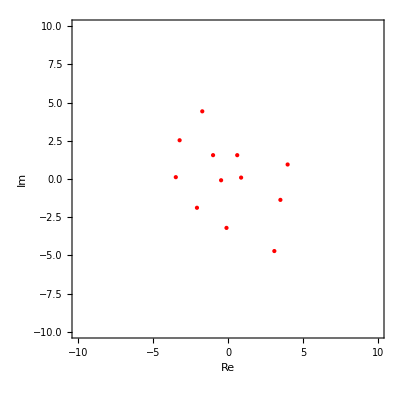

```mathematica
a=CoefficientList[Series[Exp[z  ϵ+ ⅈ ϵ^2 +ⅈ ϵ^4 +ⅈ ϵ^5 +  ⅈ ϵ^7  +(5ⅈ)/11  ϵ^8 + (5ⅈ)/13  ϵ^10],{ϵ,0,10}],ϵ];
aa=Part[a,{1,2,3,4,5,6,7,8,9,10}];
aa[[0]]=0;
q =Wronskian[({aa[[2]],aa[[5]],aa[[8]]}),z]//FullSimplify;
s = Solve[q == 0,z];

rt = Flatten[Values[s]]
ComplexListPlot[rt,PlotRange->{{-10,10},{-10,10}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Red,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}]
```

{Root-2.94-3.52 ⅈRoot[{1+#1^2&,862400+448000 #1-985600 #2+123200 #2^2+448000 #1 #2^2+492800 #2^3+30800 #2^4+112000 #1 #2^4-147840 #2^5+36960 #2^6-10560 #2^7+5940 #2^8+308 #2^10+11 #2^12&},{2,1}]-2.9377315049039425,Root-2.85+3.58 ⅈRoot[{1+#1^2&,862400+448000 #1-985600 #2+123200 #2^2+448000 #1 #2^2+492800 #2^3+30800 #2^4+112000 #1 #2^4-147840 #2^5+36960 #2^6-10560 #2^7+5940 #2^8+308 #2^10+11 #2^12&},{2,2}]-2.853558445923625,Root-1.64+0.778 ⅈRoot[{1+#1^2&,862400+448000 #1-985600 #2+123200 #2^2+448000 #1 #2^2+492800 #2^3+30800 #2^4+112000 #1 #2^4-147840 #2^5+36960 #2^6-10560 #2^7+5940 #2^8+308 #2^10+11 #2^12&},{2,3}]-1.6427290292286576,Root-1.18-0.794 ⅈRoot[{1+#1^2&,862400+448000 #1-985600 #2+123200 #2^2+448000 #1 #2^2+492800 #2^3+30800 #2^4+112000 #1 #2^4-147840 #2^5+36960 #2^6-10560 #2^7+5940 #2^8+308 #2^10+11 #2^12&},{2,4}]-1.1766055072376012,Root-0.503-3.78 ⅈRoot[{1+#1^2&,862400+448000 #1-985600 #2+123200 #2^2+448000 #1 #2^2+492800 #2^3+30800 #2^4+112000 #1 #2^4-147840 #2^5+36960 #2^6-10560 #2^7+5940 #2^8+308 #2^10+11 #2^12&},{2,5}]-0.5029341188943852,Root-0.388+3.56 ⅈRoot[{1+#1^2&,862400+448000 #1-985600 #2+123200 #2^2+448000 #1 #2^2+492800 #2^3+30800 #2^4+112000 #1 #2^4-147840 #2^5+36960 #2^6-10560 #2^7+5940 #2^8+308 #2^10+11 #2^12&},{2,6}]-0.38790025992893234,Root0.468+0.563 ⅈRoot[{1+#1^2&,862400+448000 #1-985600 #2+123200 #2^2+448000 #1 #2^2+492800 #2^3+30800 #2^4+112000 #1 #2^4-147840 #2^5+36960 #2^6-10560 #2^7+5940 #2^8+308 #2^10+11 #2^12&},{2,7}]0.46770597888894216,Root0.823-0.943 ⅈRoot[{1+#1^2&,862400+448000 #1-985600 #2+123200 #2^2+448000 #1 #2^2+492800 #2^3+30800 #2^4+112000 #1 #2^4-147840 #2^5+36960 #2^6-10560 #2^7+5940 #2^8+308 #2^10+11 #2^12&},{2,8}]0.8232055812765868,Root1.84+1.24 ⅈRoot[{1+#1^2&,862400+448000 #1-985600 #2+123200 #2^2+448000 #1 #2^2+492800 #2^3+30800 #2^4+112000 #1 #2^4-147840 #2^5+36960 #2^6-10560 #2^7+5940 #2^8+308 #2^10+11 #2^12&},{2,9}]1.8361116437315406,Root1.91+4.38 ⅈRoot[{1+#1^2&,862400+448000 #1-985600 #2+123200 #2^2+448000 #1 #2^2+492800 #2^3+30800 #2^4+112000 #1 #2^4-147840 #2^5+36960 #2^6-10560 #2^7+5940 #2^8+308 #2^10+11 #2^12&},{2,10}]1.9138006948686708,Root2.00-4.42 ⅈRoot[{1+#1^2&,862400+448000 #1-985600 #2+123200 #2^2+448000 #1 #2^2+492800 #2^3+30800 #2^4+112000 #1 #2^4-147840 #2^5+36960 #2^6-10560 #2^7+5940 #2^8+308 #2^10+11 #2^12&},{2,11}]2.00433246780408,Root2.46-0.647 ⅈRoot[{1+#1^2&,862400+448000 #1-985600 #2+123200 #2^2+448000 #1 #2^2+492800 #2^3+30800 #2^4+112000 #1 #2^4-147840 #2^5+36960 #2^6-10560 #2^7+5940 #2^8+308 #2^10+11 #2^12&},{2,12}]2.456302499547323}

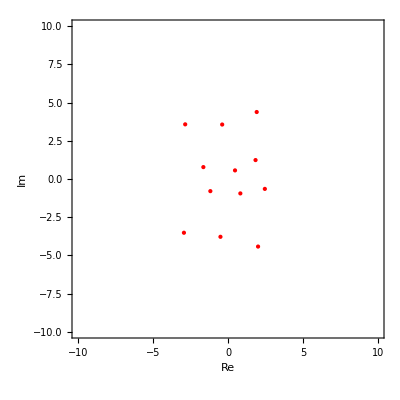

```mathematica
a=CoefficientList[Series[Exp[z  ϵ+ ϵ^2 - ϵ^4 + ϵ^5 -   ϵ^7  +(5ⅈ)/11  ϵ^8 + (5ⅈ)/13  ϵ^10],{ϵ,0,10}],ϵ];
aa=Part[a,{1,2,3,4,5,6,7,8,9,10}];
aa[[0]]=0;
q =Wronskian[({aa[[2]],aa[[5]],aa[[8]]}),z]//FullSimplify;
s = Solve[q == 0,z];

rt = Flatten[Values[s]]
ComplexListPlot[rt,PlotRange->{{-10,10},{-10,10}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Red,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}]
```

```mathematica
a=CoefficientList[Series[Exp[z  ϵ+  ϵ^2 + ϵ^4 +ϵ^5 +  ϵ^7  +(5ⅈ)/11  ϵ^8 + (5ⅈ)/13  ϵ^10],{ϵ,0,10}],ϵ];
aa=Part[a,{1,2,3,4,5,6,7,8,9,10}];
aa[[0]]=0;
q =Wronskian[({aa[[2]],aa[[5]],aa[[8]]}),z]//FullSimplify;
s = Solve[q == 0,z];

rt = Flatten[Values[s]]
ComplexListPlot[rt,PlotRange->{{-10,10},{-10,10}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Red,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}]
```

{Root-2.70Root[1120-5040 #1+2240 #1^2-280 #1^4-56 #1^5+16 #1^7+#1^9&,1]-2.6974493903138073,Root0.250Root[1120-5040 #1+2240 #1^2-280 #1^4-56 #1^5+16 #1^7+#1^9&,2]0.24970870702864786,Root2.52Root[1120-5040 #1+2240 #1^2-280 #1^4-56 #1^5+16 #1^7+#1^9&,3]2.515766393410886,Root-1.79-2.48 ⅈRoot[1120-5040 #1+2240 #1^2-280 #1^4-56 #1^5+16 #1^7+#1^9&,4]-1.790037527891566,Root-1.79+2.48 ⅈRoot[1120-5040 #1+2240 #1^2-280 #1^4-56 #1^5+16 #1^7+#1^9&,5]-1.790037527891566,Root0.361-4.52 ⅈRoot[1120-5040 #1+2240 #1^2-280 #1^4-56 #1^5+16 #1^7+#1^9&,6]0.360592027959151,Root0.361+4.52 ⅈRoot[1120-5040 #1+2240 #1^2-280 #1^4-56 #1^5+16 #1^7+#1^9&,7]0.360592027959151,Root1.40-1.21 ⅈRoot[1120-5040 #1+2240 #1^2-280 #1^4-56 #1^5+16 #1^7+#1^9&,8]1.395432644869552,Root1.40+1.21 ⅈRoot[1120-5040 #1+2240 #1^2-280 #1^4-56 #1^5+16 #1^7+#1^9&,9]1.395432644869552}

-Graphics-

```mathematica
a=CoefficientList[Series[Exp[z  ϵ+  ϵ^2 + 4 ϵ^4 +7 ϵ^5 +  2 ϵ^7  +(5ⅈ)/11  ϵ^8 + (5ⅈ)/13  ϵ^10],{ϵ,0,10}],ϵ];
aa=Part[a,{1,2,3,4,5,6,7,8,9,10}];
aa[[0]]=0;
q =Wronskian[({aa[[2]],aa[[5]],aa[[8]]}),z]//FullSimplify;
s = Solve[q == 0,z];

rt = Flatten[Values[s]]
ComplexListPlot[rt,PlotRange->{{-10,10},{-10,10}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Red,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}]
```

{Root-3.37Root[-50400-45360 #1+10080 #1^2-1960 #1^4-392 #1^5+16 #1^7+#1^9&,1]-3.3679116849150312,Root-0.942Root[-50400-45360 #1+10080 #1^2-1960 #1^4-392 #1^5+16 #1^7+#1^9&,2]-0.9418301494893117,Root4.68Root[-50400-45360 #1+10080 #1^2-1960 #1^4-392 #1^5+16 #1^7+#1^9&,3]4.67901128679977,Root-2.70-2.82 ⅈRoot[-50400-45360 #1+10080 #1^2-1960 #1^4-392 #1^5+16 #1^7+#1^9&,4]-2.701620819848673,Root-2.70+2.82 ⅈRoot[-50400-45360 #1+10080 #1^2-1960 #1^4-392 #1^5+16 #1^7+#1^9&,5]-2.701620819848673,Root0.658-5.76 ⅈRoot[-50400-45360 #1+10080 #1^2-1960 #1^4-392 #1^5+16 #1^7+#1^9&,6]0.6578216272907005,Root0.658+5.76 ⅈRoot[-50400-45360 #1+10080 #1^2-1960 #1^4-392 #1^5+16 #1^7+#1^9&,7]0.6578216272907005,Root1.86-1.78 ⅈRoot[-50400-45360 #1+10080 #1^2-1960 #1^4-392 #1^5+16 #1^7+#1^9&,8]1.859164466360259,Root1.86+1.78 ⅈRoot[-50400-45360 #1+10080 #1^2-1960 #1^4-392 #1^5+16 #1^7+#1^9&,9]1.859164466360259}

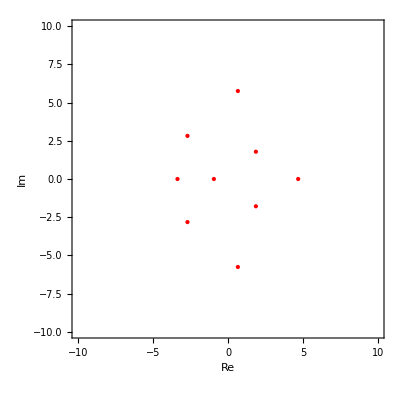

```mathematica
a=CoefficientList[Series[Exp[z  ϵ+  ⅈ ϵ^2 +ⅈ ϵ^4 +ⅈ ϵ^5 +ⅈ ϵ^7  +((5ⅈ)/11)  ϵ^8 + ((5ⅈ)/13)  ϵ^10],{ϵ,0,10}],ϵ];
aa=Part[a,{1,2,3,4,5,6,7,8,9,10}];
aa[[0]]=0;
q =Wronskian[({aa[[2]],aa[[5]],aa[[8]]}),z]//FullSimplify;
s = Solve[q == 0,z];

rt = Flatten[Values[s]]
ComplexListPlot[rt,PlotRange->{{-10,10},{-10,10}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Red,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}]
```

{Root-2.74+1.51 ⅈRoot[{1+#1^2&,-1120 #1+1680 #2+2240 #1 #2-1120 #2^2+1120 #1 #2^2-280 #1 #2^4-56 #2^5-112 #1 #2^5+16 #1 #2^7+#2^9&},{2,1}]-2.7434190851017353,Root-2.41-0.746 ⅈRoot[{1+#1^2&,-1120 #1+1680 #2+2240 #1 #2-1120 #2^2+1120 #1 #2^2-280 #1 #2^4-56 #2^5-112 #1 #2^5+16 #1 #2^7+#2^9&},{2,2}]-2.410363490937923,Root-1.71+3.50 ⅈRoot[{1+#1^2&,-1120 #1+1680 #2+2240 #1 #2-1120 #2^2+1120 #1 #2^2-280 #1 #2^4-56 #2^5-112 #1 #2^5+16 #1 #2^7+#2^9&},{2,3}]-1.7138762043292037,Root-0.624-2.36 ⅈRoot[{1+#1^2&,-1120 #1+1680 #2+2240 #1 #2-1120 #2^2+1120 #1 #2^2-280 #1 #2^4-56 #2^5-112 #1 #2^5+16 #1 #2^7+#2^9&},{2,4}]-0.6242820766380841,Root-0.431+1.21 ⅈRoot[{1+#1^2&,-1120 #1+1680 #2+2240 #1 #2-1120 #2^2+1120 #1 #2^2-280 #1 #2^4-56 #2^5-112 #1 #2^5+16 #1 #2^7+#2^9&},{2,5}]-0.4308107123206048,Root0.380+0.167 ⅈRoot[{1+#1^2&,-1120 #1+1680 #2+2240 #1 #2-1120 #2^2+1120 #1 #2^2-280 #1 #2^4-56 #2^5-112 #1 #2^5+16 #1 #2^7+#2^9&},{2,6}]0.37959286292487837,Root2.03+0.466 ⅈRoot[{1+#1^2&,-1120 #1+1680 #2+2240 #1 #2-1120 #2^2+1120 #1 #2^2-280 #1 #2^4-56 #2^5-112 #1 #2^5+16 #1 #2^7+#2^9&},{2,7}]2.0263517030867026,Root2.56-3.75 ⅈRoot[{1+#1^2&,-1120 #1+1680 #2+2240 #1 #2-1120 #2^2+1120 #1 #2^2-280 #1 #2^4-56 #2^5-112 #1 #2^5+16 #1 #2^7+#2^9&},{2,8}]2.556170217123145,Root2.96-8.95 × 10^-3 ⅈRoot[{1+#1^2&,-1120 #1+1680 #2+2240 #1 #2-1120 #2^2+1120 #1 #2^2-280 #1 #2^4-56 #2^5-112 #1 #2^5+16 #1 #2^7+#2^9&},{2,9}]2.9606367861928247}

-Graphics-

{-ⅈ √2,ⅈ √2,Root-1.36Root[560-280 #1-280 #1^2+140 #1^3+14 #1^5+#1^7&,1]-1.3580557569964378,Root-2.03-3.07 ⅈRoot[560-280 #1-280 #1^2+140 #1^3+14 #1^5+#1^7&,2]-2.0291352941912546,Root-2.03+3.07 ⅈRoot[560-280 #1-280 #1^2+140 #1^3+14 #1^5+#1^7&,3]-2.0291352941912546,Root1.32-3.63 ⅈRoot[560-280 #1-280 #1^2+140 #1^3+14 #1^5+#1^7&,4]1.3201807918905462,Root1.32+3.63 ⅈRoot[560-280 #1-280 #1^2+140 #1^3+14 #1^5+#1^7&,5]1.3201807918905462,Root1.39-0.340 ⅈRoot[560-280 #1-280 #1^2+140 #1^3+14 #1^5+#1^7&,6]1.387982380798927,Root1.39+0.340 ⅈRoot[560-280 #1-280 #1^2+140 #1^3+14 #1^5+#1^7&,7]1.387982380798927}

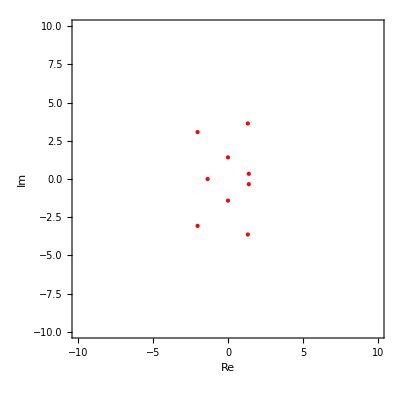

```mathematica
a=CoefficientList[Series[Exp[z  ϵ+   ϵ^2 - ϵ^4 + ϵ^5 - ϵ^7  +(5ⅈ)/11  ϵ^8 + (5ⅈ)/13  ϵ^10],{ϵ,0,10}],ϵ];
aa=Part[a,{1,2,3,4,5,6,7,8,9,10}];
aa[[0]]=0;
q =Wronskian[({aa[[2]],aa[[5]],aa[[8]]}),z]//FullSimplify;
s = Solve[q == 0,z];

rt = Flatten[Values[s]]
ComplexListPlot[rt,PlotRange->{{-10,10},{-10,10}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Red,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}]
```

{Root-3.36+1.97 ⅈRoot[{1+#1^2&,-1120 #1-560 #2-1120 #2^2-280 #1 #2^4-56 #2^5+16 #1 #2^7+#2^9&},{2,1}]-3.3626196167332276,Root-1.64-0.966 ⅈRoot[{1+#1^2&,-1120 #1-560 #2-1120 #2^2-280 #1 #2^4-56 #2^5+16 #1 #2^7+#2^9&},{2,2}]-1.6399243674502906,Root-1.09+3.29 ⅈRoot[{1+#1^2&,-1120 #1-560 #2-1120 #2^2-280 #1 #2^4-56 #2^5+16 #1 #2^7+#2^9&},{2,3}]-1.0903558656453145,Root-0.811+0.647 ⅈRoot[{1+#1^2&,-1120 #1-560 #2-1120 #2^2-280 #1 #2^4-56 #2^5+16 #1 #2^7+#2^9&},{2,4}]-0.8108724692485184,Root-0.431-2.27 ⅈRoot[{1+#1^2&,-1120 #1-560 #2-1120 #2^2-280 #1 #2^4-56 #2^5+16 #1 #2^7+#2^9&},{2,5}]-0.43129038197366176,Root0.477-0.639 ⅈRoot[{1+#1^2&,-1120 #1-560 #2-1120 #2^2-280 #1 #2^4-56 #2^5+16 #1 #2^7+#2^9&},{2,6}]0.4765573899611784,Root1.23+1.39 ⅈRoot[{1+#1^2&,-1120 #1-560 #2-1120 #2^2-280 #1 #2^4-56 #2^5+16 #1 #2^7+#2^9&},{2,7}]1.2281834740005477,Root2.69-3.17 ⅈRoot[{1+#1^2&,-1120 #1-560 #2-1120 #2^2-280 #1 #2^4-56 #2^5+16 #1 #2^7+#2^9&},{2,8}]2.6884555447814895,Root2.94-0.248 ⅈRoot[{1+#1^2&,-1120 #1-560 #2-1120 #2^2-280 #1 #2^4-56 #2^5+16 #1 #2^7+#2^9&},{2,9}]2.9418662923077976}

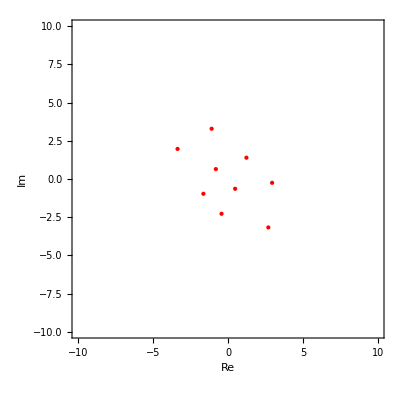

```mathematica
a=CoefficientList[Series[Exp[z  ϵ+  ⅈ ϵ^2 +ⅈ ϵ^5   +(5ⅈ)/11  ϵ^8 + (5ⅈ)/13  ϵ^10],{ϵ,0,10}],ϵ];
aa=Part[a,{1,2,3,4,5,6,7,8,9,10}];
aa[[0]]=0;
q =Wronskian[({aa[[2]],aa[[5]],aa[[8]]}),z]//FullSimplify;
s = Solve[q == 0,z];

rt = Flatten[Values[s]]
ComplexListPlot[rt,PlotRange->{{-10,10},{-10,10}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Red,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}]
```

{0,Root-2.53+0.655 ⅈRoot[{1+#1^2&,1680+2240 #1-56 #2^4-112 #1 #2^4+16 #1 #2^6+#2^8&},{2,1}]-2.5297501719088715,Root-2.37-0.573 ⅈRoot[{1+#1^2&,1680+2240 #1-56 #2^4-112 #1 #2^4+16 #1 #2^6+#2^8&},{2,2}]-2.3727596924049625,Root-2.27+3.55 ⅈRoot[{1+#1^2&,1680+2240 #1-56 #2^4-112 #1 #2^4+16 #1 #2^6+#2^8&},{2,3}]-2.2675639581164213,Root-0.175-1.96 ⅈRoot[{1+#1^2&,1680+2240 #1-56 #2^4-112 #1 #2^4+16 #1 #2^6+#2^8&},{2,4}]-0.17475706870511146,Root0.175+1.96 ⅈRoot[{1+#1^2&,1680+2240 #1-56 #2^4-112 #1 #2^4+16 #1 #2^6+#2^8&},{2,5}]0.17475706870511146,Root2.27-3.55 ⅈRoot[{1+#1^2&,1680+2240 #1-56 #2^4-112 #1 #2^4+16 #1 #2^6+#2^8&},{2,6}]2.2675639581164213,Root2.37+0.573 ⅈRoot[{1+#1^2&,1680+2240 #1-56 #2^4-112 #1 #2^4+16 #1 #2^6+#2^8&},{2,7}]2.3727596924049625,Root2.53-0.655 ⅈRoot[{1+#1^2&,1680+2240 #1-56 #2^4-112 #1 #2^4+16 #1 #2^6+#2^8&},{2,8}]2.5297501719088715}

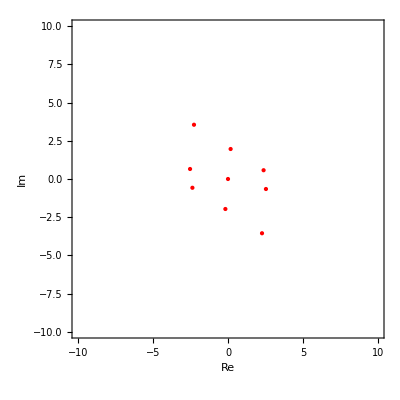

```mathematica
a=CoefficientList[Series[Exp[z  ϵ+ⅈ ϵ^2+ⅈ ϵ^4   +(5ⅈ)/11  ϵ^8 + (5ⅈ)/13  ϵ^10],{ϵ,0,10}],ϵ];
aa=Part[a,{1,2,3,4,5,6,7,8,9,10}];
aa[[0]]=0;
q =Wronskian[({aa[[2]],aa[[5]],aa[[8]]}),z]//FullSimplify;
s = Solve[q == 0,z];

rt = Flatten[Values[s]]
ComplexListPlot[rt,PlotRange->{{-10,10},{-10,10}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Red,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}]
```

```mathematica
a=CoefficientList[Series[Exp[z  ϵ+1 ϵ^2+1 ϵ^4+1 ϵ^5 +1 ϵ^7 +(5ⅈ)/11  ϵ^8 + (5ⅈ)/13  ϵ^10],{ϵ,0,10}],ϵ];
aa=Part[a,{1,2,3,4,5,6,7,8,9,10}];
aa[[0]]=0;
q =Wronskian[({aa[[2]],aa[[5]],aa[[8]]}),z]//FullSimplify;
s = Solve[q == 0,z];

rt = Flatten[Values[s]]
ComplexListPlot[rt,PlotRange->{{-10,10},{-10,10}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Red,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}]
```

{Root-2.70Root[1120-5040 #1+2240 #1^2-280 #1^4-56 #1^5+16 #1^7+#1^9&,1]-2.6974493903138073,Root0.250Root[1120-5040 #1+2240 #1^2-280 #1^4-56 #1^5+16 #1^7+#1^9&,2]0.2497087070286478,Root2.52Root[1120-5040 #1+2240 #1^2-280 #1^4-56 #1^5+16 #1^7+#1^9&,3]2.515766393410886,Root-1.79-2.48 ⅈRoot[1120-5040 #1+2240 #1^2-280 #1^4-56 #1^5+16 #1^7+#1^9&,4]-1.7900375278915661,Root-1.79+2.48 ⅈRoot[1120-5040 #1+2240 #1^2-280 #1^4-56 #1^5+16 #1^7+#1^9&,5]-1.7900375278915661,Root0.361-4.52 ⅈRoot[1120-5040 #1+2240 #1^2-280 #1^4-56 #1^5+16 #1^7+#1^9&,6]0.36059202795915096,Root0.361+4.52 ⅈRoot[1120-5040 #1+2240 #1^2-280 #1^4-56 #1^5+16 #1^7+#1^9&,7]0.36059202795915096,Root1.40-1.21 ⅈRoot[1120-5040 #1+2240 #1^2-280 #1^4-56 #1^5+16 #1^7+#1^9&,8]1.3954326448695518,Root1.40+1.21 ⅈRoot[1120-5040 #1+2240 #1^2-280 #1^4-56 #1^5+16 #1^7+#1^9&,9]1.3954326448695518}

-Graphics-

{Root-4.30Root[-40320-181440 #1+10080 #1^2-1120 #1^4-560 #1^5+32 #1^7+#1^9&,1]-4.296346339302396,Root-0.220Root[-40320-181440 #1+10080 #1^2-1120 #1^4-560 #1^5+32 #1^7+#1^9&,2]-0.21955692688157966,Root4.60Root[-40320-181440 #1+10080 #1^2-1120 #1^4-560 #1^5+32 #1^7+#1^9&,3]4.599866033734934,Root-2.53-3.15 ⅈRoot[-40320-181440 #1+10080 #1^2-1120 #1^4-560 #1^5+32 #1^7+#1^9&,4]-2.5323564251041675,Root-2.53+3.15 ⅈRoot[-40320-181440 #1+10080 #1^2-1120 #1^4-560 #1^5+32 #1^7+#1^9&,5]-2.5323564251041675,Root0.227-6.81 ⅈRoot[-40320-181440 #1+10080 #1^2-1120 #1^4-560 #1^5+32 #1^7+#1^9&,6]0.2272658222382098,Root0.227+6.81 ⅈRoot[-40320-181440 #1+10080 #1^2-1120 #1^4-560 #1^5+32 #1^7+#1^9&,7]0.2272658222382098,Root2.26-2.67 ⅈRoot[-40320-181440 #1+10080 #1^2-1120 #1^4-560 #1^5+32 #1^7+#1^9&,8]2.2631092190904782,Root2.26+2.67 ⅈRoot[-40320-181440 #1+10080 #1^2-1120 #1^4-560 #1^5+32 #1^7+#1^9&,9]2.2631092190904782}

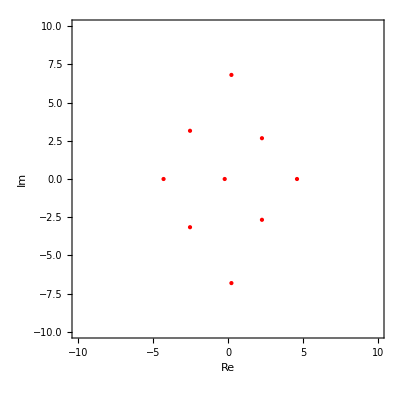

```mathematica
a=CoefficientList[Series[Exp[z  ϵ+ 2ϵ^2+7 ϵ^4 +4ϵ^5+1 ϵ^7   +(5ⅈ)/11  ϵ^8 + (5ⅈ)/13  ϵ^10],{ϵ,0,10}],ϵ];
aa=Part[a,{1,2,3,4,5,6,7,8,9,10}];
aa[[0]]=0;
q =Wronskian[({aa[[2]],aa[[5]],aa[[8]]}),z]//FullSimplify;
s = Solve[q == 0,z];

rt = Flatten[Values[s]]
ComplexListPlot[rt,PlotRange->{{-10,10},{-10,10}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Red,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}]
```

```mathematica
a=CoefficientList[Series[Exp[z  ϵ+ ϵ^2+4ϵ^4 +7ϵ^5+2ϵ^7   +(5ⅈ)/11  ϵ^8 + (5ⅈ)/13  ϵ^10],{ϵ,0,10}],ϵ];
aa=Part[a,{1,2,3,4,5,6,7,8,9,10}];
aa[[0]]=0;
q =Wronskian[({aa[[2]],aa[[5]],aa[[8]]}),z]//FullSimplify;
s = Solve[q == 0,z];

rt = Flatten[Values[s]]
ComplexListPlot[rt,PlotRange->{{-10,10},{-10,10}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Red,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}]
```

{Root-3.37Root[-50400-45360 #1+10080 #1^2-1960 #1^4-392 #1^5+16 #1^7+#1^9&,1]-3.3679116849150312,Root-0.942Root[-50400-45360 #1+10080 #1^2-1960 #1^4-392 #1^5+16 #1^7+#1^9&,2]-0.9418301494893117,Root4.68Root[-50400-45360 #1+10080 #1^2-1960 #1^4-392 #1^5+16 #1^7+#1^9&,3]4.67901128679977,Root-2.70-2.82 ⅈRoot[-50400-45360 #1+10080 #1^2-1960 #1^4-392 #1^5+16 #1^7+#1^9&,4]-2.701620819848673,Root-2.70+2.82 ⅈRoot[-50400-45360 #1+10080 #1^2-1960 #1^4-392 #1^5+16 #1^7+#1^9&,5]-2.701620819848673,Root0.658-5.76 ⅈRoot[-50400-45360 #1+10080 #1^2-1960 #1^4-392 #1^5+16 #1^7+#1^9&,6]0.6578216272907005,Root0.658+5.76 ⅈRoot[-50400-45360 #1+10080 #1^2-1960 #1^4-392 #1^5+16 #1^7+#1^9&,7]0.6578216272907005,Root1.86-1.78 ⅈRoot[-50400-45360 #1+10080 #1^2-1960 #1^4-392 #1^5+16 #1^7+#1^9&,8]1.859164466360259,Root1.86+1.78 ⅈRoot[-50400-45360 #1+10080 #1^2-1960 #1^4-392 #1^5+16 #1^7+#1^9&,9]1.859164466360259}

-Graphics-

```mathematica
a=CoefficientList[Series[Exp[z  ϵ+2Exp[ⅈ 1/2 Pi] ϵ^2 -4Exp[ⅈ 1/4 Pi]ϵ^4 +5Exp[ⅈ 1/5 Pi]ϵ^5 -7Exp[ⅈ 1/7 Pi] ϵ^7  + (1+ⅈ)ϵ^8 - (1+ⅈ) ϵ^10],{ϵ,0,10}],ϵ];
aa=Part[a,{1,2,3,4,5,6,7,8,9,10}];
aa[[0]]=0;
q =Wronskian[({aa[[2]],aa[[5]],aa[[8]]}),z]//FullSimplify;
s = Solve[q == 0,z];

rt = Flatten[Values[s]]
ComplexListPlot[rt,PlotRange->{{-10,10},{-10,10}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Red,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}]
```

{Root-5.22+3.88 ⅈRoot[{1+#1^4-#1^20-#1^24-#1^28-#1^32+#1^40+#1^44+#1^48+#1^52+#1^56-#1^64-#1^68-#1^72-#1^76+#1^92+#1^96&,1+#2^2&,-22400 #1^28+44800 #1^63-31360 #1^90-8960 #3-35840 #1^35 #3-35840 #2 #3-11200 #1^2 #3^2-11200 #1^6 #3^2-7840 #1^20 #3^2+11200 #1^22 #3^2+11200 #1^26 #3^2+11200 #1^30 #3^2+11200 #1^34 #3^2-11200 #1^42 #3^2-11200 #1^46 #3^2-11200 #1^50 #3^2-11200 #1^54 #3^2-11200 #1^58 #3^2+11200 #1^66 #3^2+11200 #1^70 #3^2+11200 #1^74 #3^2+11200 #1^78 #3^2-11200 #1^94 #3^2-1400 #1^28 #3^4-224 #3^5+448 #1^35 #3^5+32 #2 #3^7+#3^9&},{96,2,1}]-5.215136887110341,Root-2.90-0.458 ⅈRoot[{1+#1^4-#1^20-#1^24-#1^28-#1^32+#1^40+#1^44+#1^48+#1^52+#1^56-#1^64-#1^68-#1^72-#1^76+#1^92+#1^96&,1+#2^2&,-22400 #1^28+44800 #1^63-31360 #1^90-8960 #3-35840 #1^35 #3-35840 #2 #3-11200 #1^2 #3^2-11200 #1^6 #3^2-7840 #1^20 #3^2+11200 #1^22 #3^2+11200 #1^26 #3^2+11200 #1^30 #3^2+11200 #1^34 #3^2-11200 #1^42 #3^2-11200 #1^46 #3^2-11200 #1^50 #3^2-11200 #1^54 #3^2-11200 #1^58 #3^2+11200 #1^66 #3^2+11200 #1^70 #3^2+11200 #1^74 #3^2+11200 #1^78 #3^2-11200 #1^94 #3^2-1400 #1^28 #3^4-224 #3^5+448 #1^35 #3^5+32 #2 #3^7+#3^9&},{96,2,2}]-2.9017520223492514,Root-2.01-3.12 ⅈRoot[{1+#1^4-#1^20-#1^24-#1^28-#1^32+#1^40+#1^44+#1^48+#1^52+#1^56-#1^64-#1^68-#1^72-#1^76+#1^92+#1^96&,1+#2^2&,-22400 #1^28+44800 #1^63-31360 #1^90-8960 #3-35840 #1^35 #3-35840 #2 #3-11200 #1^2 #3^2-11200 #1^6 #3^2-7840 #1^20 #3^2+11200 #1^22 #3^2+11200 #1^26 #3^2+11200 #1^30 #3^2+11200 #1^34 #3^2-11200 #1^42 #3^2-11200 #1^46 #3^2-11200 #1^50 #3^2-11200 #1^54 #3^2-11200 #1^58 #3^2+11200 #1^66 #3^2+11200 #1^70 #3^2+11200 #1^74 #3^2+11200 #1^78 #3^2-11200 #1^94 #3^2-1400 #1^28 #3^4-224 #3^5+448 #1^35 #3^5+32 #2 #3^7+#3^9&},{96,2,3}]-2.01491832296382,Root-0.605+4.14 ⅈRoot[{1+#1^4-#1^20-#1^24-#1^28-#1^32+#1^40+#1^44+#1^48+#1^52+#1^56-#1^64-#1^68-#1^72-#1^76+#1^92+#1^96&,1+#2^2&,-22400 #1^28+44800 #1^63-31360 #1^90-8960 #3-35840 #1^35 #3-35840 #2 #3-11200 #1^2 #3^2-11200 #1^6 #3^2-7840 #1^20 #3^2+11200 #1^22 #3^2+11200 #1^26 #3^2+11200 #1^30 #3^2+11200 #1^34 #3^2-11200 #1^42 #3^2-11200 #1^46 #3^2-11200 #1^50 #3^2-11200 #1^54 #3^2-11200 #1^58 #3^2+11200 #1^66 #3^2+11200 #1^70 #3^2+11200 #1^74 #3^2+11200 #1^78 #3^2-11200 #1^94 #3^2-1400 #1^28 #3^4-224 #3^5+448 #1^35 #3^5+32 #2 #3^7+#3^9&},{96,2,4}]-0.6053582506374574,Root0.0527-0.0107 ⅈRoot[{1+#1^4-#1^20-#1^24-#1^28-#1^32+#1^40+#1^44+#1^48+#1^52+#1^56-#1^64-#1^68-#1^72-#1^76+#1^92+#1^96&,1+#2^2&,-22400 #1^28+44800 #1^63-31360 #1^90-8960 #3-35840 #1^35 #3-35840 #2 #3-11200 #1^2 #3^2-11200 #1^6 #3^2-7840 #1^20 #3^2+11200 #1^22 #3^2+11200 #1^26 #3^2+11200 #1^30 #3^2+11200 #1^34 #3^2-11200 #1^42 #3^2-11200 #1^46 #3^2-11200 #1^50 #3^2-11200 #1^54 #3^2-11200 #1^58 #3^2+11200 #1^66 #3^2+11200 #1^70 #3^2+11200 #1^74 #3^2+11200 #1^78 #3^2-11200 #1^94 #3^2-1400 #1^28 #3^4-224 #3^5+448 #1^35 #3^5+32 #2 #3^7+#3^9&},{96,2,5}]0.0527139374116413,Root0.812-2.75 ⅈRoot[{1+#1^4-#1^20-#1^24-#1^28-#1^32+#1^40+#1^44+#1^48+#1^52+#1^56-#1^64-#1^68-#1^72-#1^76+#1^92+#1^96&,1+#2^2&,-22400 #1^28+44800 #1^63-31360 #1^90-8960 #3-35840 #1^35 #3-35840 #2 #3-11200 #1^2 #3^2-11200 #1^6 #3^2-7840 #1^20 #3^2+11200 #1^22 #3^2+11200 #1^26 #3^2+11200 #1^30 #3^2+11200 #1^34 #3^2-11200 #1^42 #3^2-11200 #1^46 #3^2-11200 #1^50 #3^2-11200 #1^54 #3^2-11200 #1^58 #3^2+11200 #1^66 #3^2+11200 #1^70 #3^2+11200 #1^74 #3^2+11200 #1^78 #3^2-11200 #1^94 #3^2-1400 #1^28 #3^4-224 #3^5+448 #1^35 #3^5+32 #2 #3^7+#3^9&},{96,2,6}]0.8118535970047038,Root1.79+3.13 ⅈRoot[{1+#1^4-#1^20-#1^24-#1^28-#1^32+#1^40+#1^44+#1^48+#1^52+#1^56-#1^64-#1^68-#1^72-#1^76+#1^92+#1^96&,1+#2^2&,-22400 #1^28+44800 #1^63-31360 #1^90-8960 #3-35840 #1^35 #3-35840 #2 #3-11200 #1^2 #3^2-11200 #1^6 #3^2-7840 #1^20 #3^2+11200 #1^22 #3^2+11200 #1^26 #3^2+11200 #1^30 #3^2+11200 #1^34 #3^2-11200 #1^42 #3^2-11200 #1^46 #3^2-11200 #1^50 #3^2-11200 #1^54 #3^2-11200 #1^58 #3^2+11200 #1^66 #3^2+11200 #1^70 #3^2+11200 #1^74 #3^2+11200 #1^78 #3^2-11200 #1^94 #3^2-1400 #1^28 #3^4-224 #3^5+448 #1^35 #3^5+32 #2 #3^7+#3^9&},{96,2,7}]1.7925842918322004,Root3.79-0.716 ⅈRoot[{1+#1^4-#1^20-#1^24-#1^28-#1^32+#1^40+#1^44+#1^48+#1^52+#1^56-#1^64-#1^68-#1^72-#1^76+#1^92+#1^96&,1+#2^2&,-22400 #1^28+44800 #1^63-31360 #1^90-8960 #3-35840 #1^35 #3-35840 #2 #3-11200 #1^2 #3^2-11200 #1^6 #3^2-7840 #1^20 #3^2+11200 #1^22 #3^2+11200 #1^26 #3^2+11200 #1^30 #3^2+11200 #1^34 #3^2-11200 #1^42 #3^2-11200 #1^46 #3^2-11200 #1^50 #3^2-11200 #1^54 #3^2-11200 #1^58 #3^2+11200 #1^66 #3^2+11200 #1^70 #3^2+11200 #1^74 #3^2+11200 #1^78 #3^2-11200 #1^94 #3^2-1400 #1^28 #3^4-224 #3^5+448 #1^35 #3^5+32 #2 #3^7+#3^9&},{96,2,8}]3.792095487871677,Root4.29-4.09 ⅈRoot[{1+#1^4-#1^20-#1^24-#1^28-#1^32+#1^40+#1^44+#1^48+#1^52+#1^56-#1^64-#1^68-#1^72-#1^76+#1^92+#1^96&,1+#2^2&,-22400 #1^28+44800 #1^63-31360 #1^90-8960 #3-35840 #1^35 #3-35840 #2 #3-11200 #1^2 #3^2-11200 #1^6 #3^2-7840 #1^20 #3^2+11200 #1^22 #3^2+11200 #1^26 #3^2+11200 #1^30 #3^2+11200 #1^34 #3^2-11200 #1^42 #3^2-11200 #1^46 #3^2-11200 #1^50 #3^2-11200 #1^54 #3^2-11200 #1^58 #3^2+11200 #1^66 #3^2+11200 #1^70 #3^2+11200 #1^74 #3^2+11200 #1^78 #3^2-11200 #1^94 #3^2-1400 #1^28 #3^4-224 #3^5+448 #1^35 #3^5+32 #2 #3^7+#3^9&},{96,2,9}]4.287918168940648}

-Graphics-

{Root-4.27Root[49280-504000 #1+14560 #1^2-560 #1^4+112 #1^5+64 #1^7+#1^9&,1]-4.2680623942724285,Root0.0981Root[49280-504000 #1+14560 #1^2-560 #1^4+112 #1^5+64 #1^7+#1^9&,2]0.09805543997694145,Root4.19Root[49280-504000 #1+14560 #1^2-560 #1^4+112 #1^5+64 #1^7+#1^9&,3]4.185072776703144,Root-2.51-4.00 ⅈRoot[49280-504000 #1+14560 #1^2-560 #1^4+112 #1^5+64 #1^7+#1^9&,4]-2.511823568192511,Root-2.51+4.00 ⅈRoot[49280-504000 #1+14560 #1^2-560 #1^4+112 #1^5+64 #1^7+#1^9&,5]-2.511823568192511,Root0.0884-8.01 ⅈRoot[49280-504000 #1+14560 #1^2-560 #1^4+112 #1^5+64 #1^7+#1^9&,6]0.08838413967970081,Root0.0884+8.01 ⅈRoot[49280-504000 #1+14560 #1^2-560 #1^4+112 #1^5+64 #1^7+#1^9&,7]0.08838413967970081,Root2.42-3.71 ⅈRoot[49280-504000 #1+14560 #1^2-560 #1^4+112 #1^5+64 #1^7+#1^9&,8]2.415906517308981,Root2.42+3.71 ⅈRoot[49280-504000 #1+14560 #1^2-560 #1^4+112 #1^5+64 #1^7+#1^9&,9]2.415906517308981}

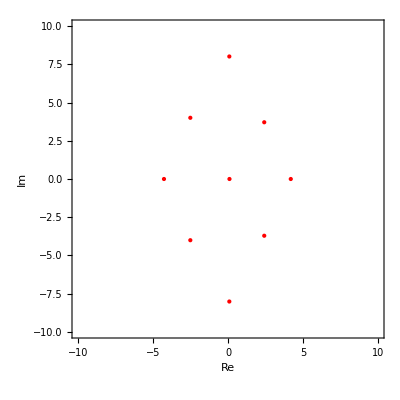

```mathematica
a=CoefficientList[Series[Exp[z  ϵ+ 4ϵ^2+7ϵ^4 +2ϵ^5+5ϵ^7   +(5ⅈ)/11  ϵ^8 + (5ⅈ)/13  ϵ^10],{ϵ,0,10}],ϵ];
aa=Part[a,{1,2,3,4,5,6,7,8,9,10}];
aa[[0]]=0;
q =Wronskian[({aa[[2]],aa[[5]],aa[[8]]}),z]//FullSimplify;
s = Solve[q == 0,z];

rt = Flatten[Values[s]]
ComplexListPlot[rt,PlotRange->{{-10,10},{-10,10}},AspectRatio->1,Frame->True,FrameTicks->Automatic,PlotStyle->{Red,PointSize[Large]},Axes->False,FrameLabel->{"Re","Im"}]
```